# Cosmic-ray upscattered inelastic dark matter

This notebook contains the calculations, analysis and figures for the paper arXiv:2108.00583

## Introduction

This notebook calculates the flux and observable rates of cosmic-ray upscattered inelastic dark matter.

The halo dark matter is assumed to be in the low mass state χ_1 with mass m_χ_1, this can be upscattered to a heavier state χ_2 with mass m_χ_2=m_χ_1+δ
(m_χ_1 and δ are taken as the model parameters, m_χ_2 is not used so all refereces to mass can be assumed to be m_χ_1) 

Throughout the calculations units are generally assumed to be in GeV, except where explicitly named in the variable.

- Gray (initialization) cells can be evaluated automatically
- Red cells are the main computations and can take minutes to run
- Blue cells create plots
- Purple cells create output files

## Constants

```mathematica
ℏc=0.19732698;(*GeV fm*)
Centimeter= 1/ℏc 10^13/GeV;
𝒸=2.997925 10^8;
Second=𝒸 10^2 Centimeter;
Kilogram=𝒸^2/(1.602 10^-19)GeV/10^9;
kpc=3.086 10^21 Centimeter;
KilogramDay=(1Kilogram)(24 3600Second);
tonneYr=365250 KilogramDay;
mp=0.93827208816//SetPrecision[#,11]&;
Deff=0.997kpc;
ρX=0.3 GeV/Centimeter^3;
unitsCM2S=(Centimeter^2/cm^2)(Second/s);
amu=mp/1.00727647//SetPrecision[#,10]&;
mn=0.93956542052//SetPrecision[#,11]&;
Me=510.998950keV;
```

#### Set plot styles and custom plot functions

```mathematica
SetOptions[#,Frame->True,FrameStyle->Directive[Black,18,FontFamily->Times,Thickness[.004]],AspectRatio->1,PlotStyle->Thick,ImageSize->400]&@{Plot,LogPlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot};
SetOptions[#,Frame->True,LabelStyle->Directive[Black,16,FontFamily->Times,Thickness[.004]],AspectRatio->1,ImageSize->400]&@{Histogram,MatrixPlot};
logSpace[a_, b_, n_] := 10.0^Range[Log10[a], Log10[b], (Log10[b] - Log10[a])/(n - 1)];

topLeft[x_] := Placed[x, {Scaled[{.38, .95}], {.9, 1}}];
topRight[x_] := Placed[x,{Scaled[{.95, .95}], {.9, 1}}];
Legend//Clear;
Legend[legendList_,opt:OptionsPattern[{Position->"Right",Type->"Line",LineLegend}]] := Module[{f},
If[OptionValue[Type]=="Line",
f=LineLegend;];
If[OptionValue[Type]=="Swatch",
f=SwatchLegend;];
If[OptionValue[Position]=="Right",
   f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//topRight//Return];
If[OptionValue[Position]=="Left",
   f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//topLeft//Return];

f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//Placed[#,OptionValue[Position]]&//Return;
];

LogTicks//Clear;
LogTicks[min_,max_,step_] := Block[{lmin, lmax, t},
   lmin = Floor[Log10[min]];
   lmax = Floor[Log10[max]];
   t=0;
   Return[{Join[
      Table[{10^i, If[Mod[++t,step]==0,Superscript[10, i],Null], {0.012, 0}}, {i, Floor[lmin], Ceiling[lmax]}], (Flatten[#1, 1] &)[
       Table[{i*10^j, Null, {0.006, 0}}, {j, Floor[lmin], 
        Ceiling[lmax], 1}, {i, 0.1, 0.9, 0.1}]]], 
     Join[Table[{10^i, Null, {0.012, 0}}, {i, Floor[lmin], 
     Ceiling[lmax]}], (Flatten[#1, 1] &)[ Table[{i*10^j, Null, {0.006, 0}}, {j, Floor[lmin], Ceiling[lmax], 1}, {i, 0.1, 0.9, 0.1}]]]}  ]
];
LogTicks[min_, max_] := LogTicks[min,max,1];
```

## Cosmic-ray fluxes

### Import spectra

We will consider cosmic-ray protons and helium, define their mass, charge, atomic number and spin:

```mathematica
mi  = {mp, 4.002602*amu};
Zei = {1,2};
Ai  = {1,4};
ji  = {0.5,0};
```

Import CR flux data tables and create interpolation functions:

```mathematica
NotebookDirectory[]//SetDirectory;
protonLISdata=Import["data/TABLE_Protons_R.txt","Table"]//Drop[#,1]&;
HeLISdata=Import["data/TABLE_Helium_R.txt","Table"]//Drop[#,1]&;
dIdR={Interpolation[protonLISdata,InterpolationOrder->1],Interpolation[HeLISdata,InterpolationOrder->1]};
```

Plot raw data, which is a function of rigidity:

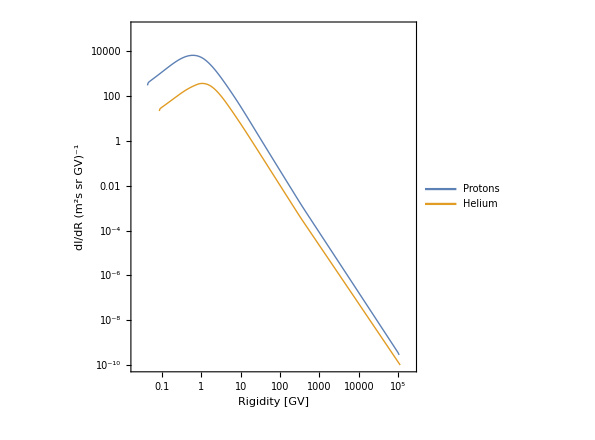

```mathematica
ListLogLogPlot[
{protonLISdata,HeLISdata},Joined->True,
FrameLabel->{"Rigidity [GV]","dI/dR (m^2s sr GV)^-1"},
PlotRange->{10^-10,10^5},
PlotLegends->Legend[{"Protons","Helium"}]]
```

### Converting to kinetic energy

Functions for rigidity (R) in terms of kinetic energy (T) and vise-versa:

```mathematica
Rt[T_,ii_]:=(√(T^2+2mi⟦ii⟧ T))/Zei⟦ii⟧
```

```mathematica
TR[R_,jj_]:=√((mi⟦jj⟧)^2+(R Zei⟦jj⟧)^2)-mi⟦jj⟧
```

Max kinetic energy in provided data files:

```mathematica
TdatMin={TR[protonLISdata⟦1,1⟧,1],TR[HeLISdata⟦1,1⟧,2]}
TdatMax={TR[protonLISdata⟦-1,1⟧,1],TR[HeLISdata⟦-1,1⟧,2]}
```

{0.000999971,0.00399668}

{105099.,420396.}

```mathematica
dRdT=D[√(T^2+2mi T),T]/Zei
```

{(1.8765441763+2 T)/(2 √(1.8765441763 T+T^2)),(7.4568+2 T)/(4 √(7.4568 T+T^2))}

Converting to function of kinetic energy and giving flux in units of GeV^2

```mathematica
dϕdT[t_?NumericQ,i_?IntegerQ]:=Evaluate[(4π)/100^2 1/(Centimeter^2 Second GeV)]dIdR⟦i⟧[Rt[t ,i]] (dRdT⟦i⟧/.T->t)
```

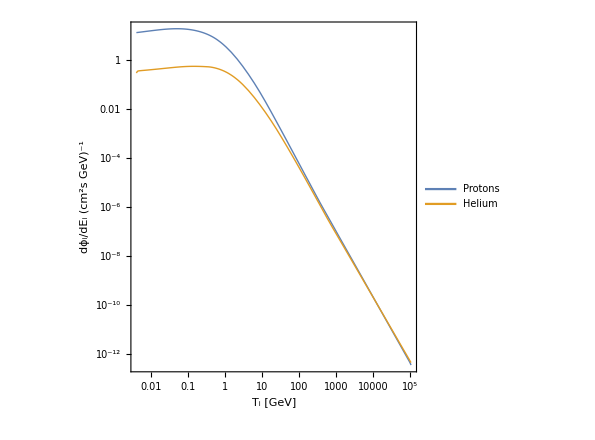

```mathematica
LogLogPlot[{Centimeter^2 Second GeVdϕdT[t,1],Centimeter^2 Second GeV dϕdT[t,2]},{t,TdatMin//Max,TdatMax//Min},FrameTicksStyle->Directive[Black,15],FrameTicks->Automatic,PlotRange->All,AspectRatio->1,PlotLegends->Legend[{"Protons","Helium"}],FrameLabel->{Style["T_i [GeV]",18,Black,FontFamily->Times],Style["dϕ_i/dE_i (cm^2s GeV)^-1",18,Black,FontFamily->Times]}]
```

Build flux tables:

```mathematica
pFlux=Table[{T,dϕdT[T,1] GeV^-2},{T,logSpace[TdatMin⟦1⟧,TdatMax⟦1⟧,800]}]//Interpolation[#,InterpolationOrder->1]&;
heFlux=Table[{T,dϕdT[T,2] GeV^-2},{T,logSpace[TdatMin⟦2⟧,TdatMax⟦2⟧,800]}]//Interpolation[#,InterpolationOrder->1]&;
```

## CRDM flux

### Kinematic limits

Find inelastic limits:

p_i= p_i'+ p_x
p_i'^2 = p_i^2+p_x^2-2 p_i p_x cosθ
use p^2=E^2-m^2 and E = T + m

```mathematica
Solve[((Tip+mii)^2-mii^2)==((Ti+mii)^2-mii^2)+((Tx+mxp)^2-mxp^2)+2 √(((Ti+mii)^2-mii^2)((Tx+mxp)^2-mxp^2))/.{mxp->mx+δ,Tip->Ti-Tx-δ},{Tx}]//FullSimplify
```

{{Tx→(2 mx Ti (2 mii+Ti)-2 (mii (mii+mx)+mx Ti) δ+(mii+mx+Ti) δ^2-√(-Ti (2 mii+Ti) (-2 mx Ti+2 (mii+mx) δ+δ^2) (2 mx (Ti-δ)-δ^2+2 mii (2 mx+δ))))/(2 (mii+mx)^2+4 mx Ti)},{Tx→(2 mx Ti (2 mii+Ti)-2 (mii (mii+mx)+mx Ti) δ+(mii+mx+Ti) δ^2+√(-Ti (2 mii+Ti) (-2 mx Ti+2 (mii+mx) δ+δ^2) (2 mx (Ti-δ)-δ^2+2 mii (2 mx+δ))))/(2 (mii+mx)^2+4 mx Ti)}}

```mathematica
1/(2 (mii)^2+4 mx Ti)(2 mx Ti (2 mii+Ti)-2 (mii (mii)+mx Ti) δ+(Ti) δ^2-√(-Ti (2 mii+Ti) (-2 mx Ti+2 (mii) δ) (2 mx (Ti)+2 mii (2 mx+δ))))//FullSimplify
```

(2 mx Ti (2 mii+Ti)-2 (mii^2+mx Ti) δ+Ti δ^2-2 √(Ti (2 mii+Ti) (mx Ti-mii δ) (mx Ti+mii (2 mx+δ))))/(2 (mii^2+2 mx Ti))

Define functions for kinematic limits:

```mathematica
TxMin[Ti_?NumericQ,mii_?NumericQ,mx_?NumericQ,δ_?NumericQ]:=
If[δ==0,0,
1/(2 (mii+mx)^2+4 mx Ti)(2 mx Ti (2 mii+Ti)-2 (mii (mii+mx)+mx Ti) δ+(mii+mx+Ti) δ^2-√(-Ti (2 mii+Ti) (-2 mx Ti+2 (mii+mx) δ+δ^2) (2 mx (Ti-δ)-δ^2+2 mii (2 mx+δ))))]
```

```mathematica
TxMax[Ti_?NumericQ,mii_?NumericQ,mx_?NumericQ,δ_?NumericQ]:=
1/(2 (mii+mx)^2+4 mx Ti)(2 mx Ti (2 mii+Ti)-2 (mii (mii+mx)+mx Ti) δ+(mii+mx+Ti) δ^2+√(-Ti (2 mii+Ti) (-2 mx Ti+2 (mii+mx) δ+δ^2) (2 mx (Ti-δ)-δ^2+2 mii (2 mx+δ))))
```

```mathematica
TxMinGlobal[mx_,δ_]:=δ^2/(2mx)
```

Minimum incoming energy to produce outgoing Tx:

```mathematica
Solve[((Tip+mii)^2-mii^2)==((Ti+mii)^2-mii^2)+((Tx+mxp)^2-mxp^2)+2 √(((Ti+mii)^2-mii^2)((Tx+mxp)^2-mxp^2))/.{mxp->mx+δ,Tip->Ti-Tx-δ},{Ti}]//FullSimplify
```

{{Ti→1/2 (-2 mii+Tx+δ+(√(Tx (2 mx+Tx+2 δ) (2 mx Tx-δ^2) (4 mii^2+2 mx Tx-δ^2)))/(-2 mx Tx+δ^2))},{Ti→1/2 (-2 mii+Tx+δ+(√(Tx (2 mx+Tx+2 δ) (2 mx Tx-δ^2) (4 mii^2+2 mx Tx-δ^2)))/(2 mx Tx-δ^2))}}

```mathematica
TiMin[Tx_?NumericQ,mii_?NumericQ,mx_?NumericQ,δ_?NumericQ]:=
If[δ>δMax[Tx,mx],∞,
1/2 (-2 mii+Tx+δ+(√(Tx (2 mx+Tx+2 δ) (2 mx Tx-δ^2) (4 mii^2+2 mx Tx-δ^2)))/(2 mx Tx-δ^2))];
```

Find max delta:

```mathematica
Solve[((16 mii mx Tx-8 mx Tx^2-8 mx Tx δ-8 mii δ^2+4 Tx δ^2+4 δ^3)^2-4 (8 mx Tx-4 δ^2) (-4 mii^2 Tx^2-8 mii mx Tx^2-4 mx^2 Tx^2-8 mii^2 Tx δ-8 mii mx Tx δ-4 mii^2 δ^2+4 mii Tx δ^2+4 mx Tx δ^2+4 mii δ^3-δ^4))==0,δ]
```

{{δ→1/2 (-2 mx-Tx)},{δ→-√2 √mx √Tx},{δ→√2 √mx √Tx},{δ→-√2 √(2 mii^2+mx Tx)},{δ→√2 √(2 mii^2+mx Tx)}}

```mathematica
δMax[Tx_,mx_]:=√(2 mx Tx)
```

Global Ti minimum:

```mathematica
gMin=D[1/2 (-2 mii+Tx+δ+(√(Tx (2 mx+Tx+2 δ) (2 mx Tx-δ^2) (4 mii^2+2 mx Tx-δ^2)))/(2 mx Tx-δ^2)),Tx]==0//Solve[#,Tx]&
```

{{Tx→((2 mii-δ) δ (mx+δ))/(2 mx (mii-mx-δ))},{Tx→(δ (2 mii+δ) (mx+δ))/(2 mx (mii+mx+δ))},{Tx→(-2 mii δ-δ^2)/(2 (mii-mx))},{Tx→(-2 mii δ+δ^2)/(2 (mii+mx))}}

```mathematica
1/2 (-2 mii+Tx+δ+(√(Tx (2 mx+Tx+2 δ) (2 mx Tx-δ^2) (4 mii^2+2 mx Tx-δ^2)))/(2 mx Tx-δ^2))/.gMin//Simplify[#,Assumptions->{mx>0,δ>0,mii>0}]&
```

{Piecewise[{{-((2 mii-δ) (2 mx+δ))/(2 mx), 2 mii≤δ⊻2 mii≤2 mx+δ}, {(mii δ (-2 mii+δ))/(2 mx (-mii+mx+δ)), True}}],(δ (2 mii+2 mx+δ))/(2 mx),Piecewise[{{-2 mii, 2 mii>2 mx+δ}, {-(δ (2 mx+δ))/(2 (mii-mx)), True}}],-((2 mii+2 mx+δ) (2 mii-δ+Abs[-2 mii+δ]))/(4 (mii+mx))}

```mathematica
TiMinGlobal[mii_?NumericQ,mx_?NumericQ,δ_?NumericQ]:=(δ (2 mii+2 mx+δ))/(2 mx)
```

Max δ for a given Ti:

```mathematica
Solve[(δ (2 mii+2 mx+δ))/(2 mx)==TiMi,δ]
```

{{δ→-mii-mx-√(mii^2+2 mii mx+mx^2+2 mx TiMi)},{δ→-mii-mx+√(mii^2+2 mii mx+mx^2+2 mx TiMi)}}

```mathematica
δMaxTi[Ti_,mii_,mx_]:=-mii-mx+√(mii^2+2 mii mx+mx^2+2 mx Ti)
```

#### Sample phase-space plots

Plot limits of kinematic variables for some example values:

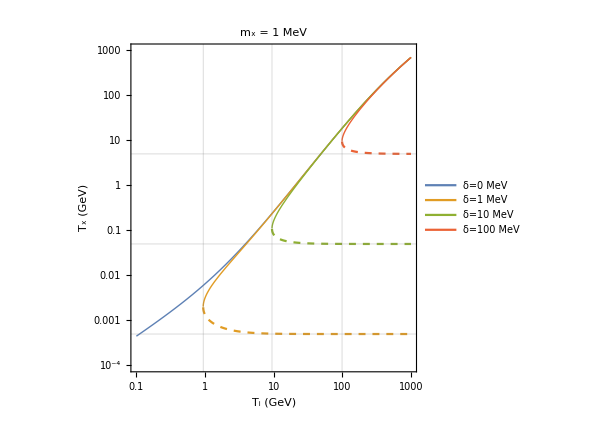
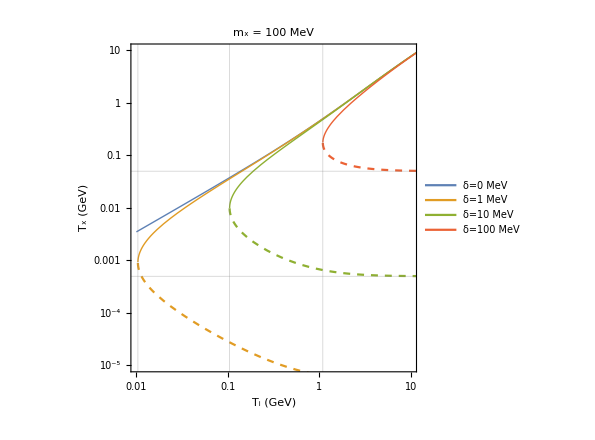

```mathematica
{Show[LogLogPlot[{TxMax[Ti,mp,.001,0],TxMax[Ti,mp,.001,0.001],TxMax[Ti,mp,.001,.01],TxMax[Ti,mp,.001,.1]},{Ti,.1,1000},FrameLabel->{"T_i (GeV)","T_x (GeV)"},PlotLabel->Style["m_x = 1 MeV",16,Black],
PlotRange->{{.1,1000},{.0001,1000}},
PlotLegends->Legend[{"δ=0 MeV","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.2,.8}],
GridLines->{{TiMinGlobal[mp,.001,.001],TiMinGlobal[mp,.001,.01],TiMinGlobal[mp,.001,.1]},{TxMinGlobal[.001,.001],TxMinGlobal[.001,.01],TxMinGlobal[.001,.1]}}],
LogLogPlot[{0,TxMin[Ti,mp,.001,0.001],TxMin[Ti,mp,.001,.01],TxMin[Ti,mp,.001,.1]},{Ti,.1,1000},PlotStyle->Dashed,FrameLabel->{"T_i (GeV)","T_x (GeV)"}]],
Show[LogLogPlot[{TxMax[Ti,mp,.1,0],TxMax[Ti,mp,.1,0.001],TxMax[Ti,mp,.1,.01],TxMax[Ti,mp,.1,.1]},{Ti,.01,50},FrameLabel->{"T_i (GeV)","T_x (GeV)"},PlotLabel->Style["m_x = 100 MeV",16,Black],
PlotRange->{{.01,10},{.00001,10}},
PlotLegends->Legend[{"δ=0 MeV","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.2,.8}],
GridLines->{{TiMinGlobal[mp,.1,.001],TiMinGlobal[mp,.1,.01],TiMinGlobal[mp,.1,.1]},{TxMinGlobal[.1,.001],TxMinGlobal[.1,.01],TxMinGlobal[.1,.1]}}],
LogLogPlot[{0,TxMin[Ti,mp,.1,0.001],TxMin[Ti,mp,.1,.01],TxMin[Ti,mp,.1,.1]},{Ti,.01,50},PlotStyle->Dashed,FrameLabel->{"T_i (GeV)","T_x (GeV)"}]]}
```

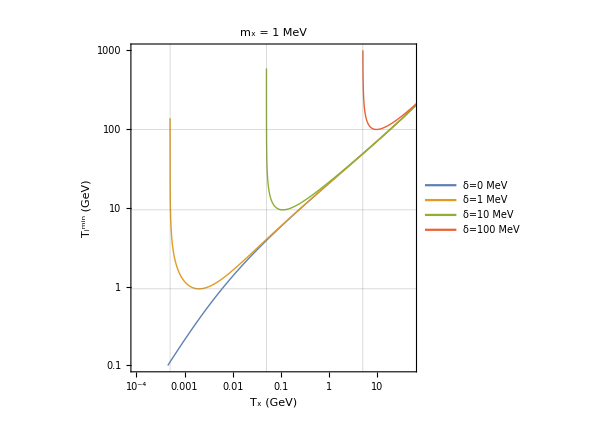
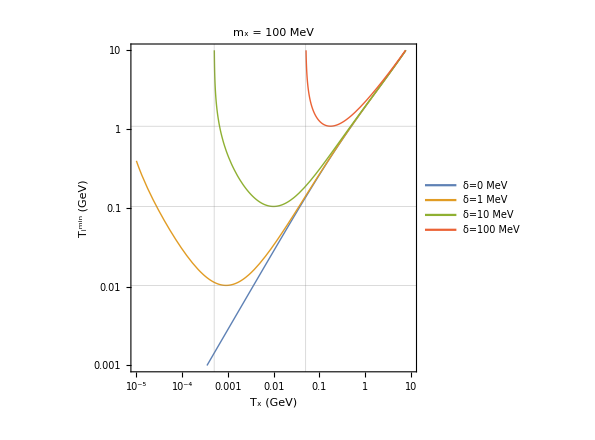

```mathematica
{LogLogPlot[{TiMin[Ti,mp,.001,0],TiMin[Ti,mp,.001,0.001],TiMin[Ti,mp,.001,.01],TiMin[Ti,mp,.001,.1]},{Ti,.0001,100},FrameLabel->{"T_x (GeV)","T_i^min (GeV)"},PlotLabel->Style["m_x = 1 MeV",16,Black],
PlotRange->{{.0001,50},{.1,1000}},
PlotLegends->Legend[{"δ=0 MeV","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.8,.2}],
GridLines->{{TxMinGlobal[.001,.001],TxMinGlobal[.001,.01],TxMinGlobal[.001,.1]},{TiMinGlobal[mp,.001,.001],TiMinGlobal[mp,.001,.01],TiMinGlobal[mp,.001,.1]}}],
LogLogPlot[{TiMin[Ti,mp,.1,0],TiMin[Ti,mp,.1,0.001],TiMin[Ti,mp,.1,.01],TiMin[Ti,mp,.1,.1]},{Ti,.00001,10},FrameLabel->{"T_x (GeV)","T_i^min (GeV)"},PlotLabel->Style["m_x = 100 MeV",16,Black],
PlotRange->{{.00001,10},{.001,10}},
PlotLegends->Legend[{"δ=0 MeV","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.8,.2}],
GridLines->{{TxMinGlobal[.1,.001],TxMinGlobal[.1,.01],TxMinGlobal[.1,.1]},{TiMinGlobal[mp,.1,.001],TiMinGlobal[mp,.1,.01],TiMinGlobal[mp,.1,.1]}}]}
```

### Form factors

#### Helm

Standard definition of the Helm form factor:
q = momentum transfer in GeV
A = atomic number of target nuclei

```mathematica
Fhelm[q_,A_]=
Piecewise[{{3(Sin[(q r)/ℏc]-((q r)/ℏc)Cos[(q r)/ℏc])/((q r)/ℏc)^3 Exp[(-((q s)/ℏc)^2)/2]/.{r->((1.23 A^(1/3)-.6)^2+7/3 π^2(0.52)^2-5(0.9)^2)^(1/2),s->0.9},4>q>0},{0,q>4}},1];
```

#### dipole form factor

Dipole form of the form factor:

```mathematica
Gi[q2_,Λi_]:=(1+q2/Λi^2)^-2
```

Where Λ comes from the charge radius:

```mathematica
Λi={0.770,0.410};
```

#### Nuclear response functions

```mathematica
WM00[qGeV_,A_]:=
Switch[A,
1,0.0397887 Gi[qGeV^2,Λi⟦1⟧]^2,
4,0.31831 Gi[qGeV^2,Λi[[2]]]^2,
_,((4π)/1 4)^-1 A^2 Fhelm[qGeV,A]^2
];
```

```mathematica
FM[qGeV_,A_,jN_]:=(4π)/(2jN+1)4WM00[qGeV,A]
```

### CR-DM cross section

Reduced mass:

```mathematica
μ[m1_,m2_]:=(m1 m2)/(m1+m2)
```

Functions for NR cross section:

```mathematica
σXP[g_,mx_,mϕ_,kk_:0]:=(4 g^4 μ[mx,mp]^2)/(π mϕ^4(1+4 kk^2/mϕ^2))/Centimeter^2/GeV^2
```

Coupling for a given cross section:

```mathematica
gg[σ_,mx_,mϕ_]:=((σ π mϕ^4)/(4 μ[mx,mp]^2)Centimeter^2 GeV^2 )^(1/4)
```

Full differential cross section (A^2 enhancement is included in the structure factor F_M):
	Tx = DM kinetic energy
	Ti  = incoming CR energy 
	mx = mass of dark matter
	δ = mass splitting
	gxi = to mediator coupling (takes x and nucleon coupling as the same)
	mA = mass of mediator
	iS = species of CR (1 = proton, 2 = neutron)
Units of returned differential cross section are GeV^-3

```mathematica
dσidTxVector[Tx_?NumericQ,Ti_?NumericQ,mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,mA_?NumericQ,iS_?IntegerQ]:=
((gxi^4 (4 mx (mi⟦iS⟧+Ti)^2-2 ((mi⟦iS⟧+mx)^2+2 mx Ti) Tx+2 mx Tx^2-4 mx (mi⟦iS⟧+Ti) δ+(mx-Tx) δ^2))
/(2 π Ti (2 mi⟦iS⟧+Ti) (mA^2+2 mx Tx-δ^2)^2 GeV^3))FM[√(2 mx Tx-δ^2),Ai⟦iS⟧,ji⟦iS⟧]
```

### Define flux

Function for the upscattered χ_2dark matter flux, contributions from protons and helium included.
	Tx2 = flux is computed for the χ_2DM kinetic energy Tx2
	mx = mass of dark matter
	δ = mass splitting
	gxi = to mediator coupling (takes x and nucleon coupling as the same)
	mA = mass of mediator
Units of returned flux are GeV^2

```mathematica
dϕX2dTx2[Tx2_?NumericQ,mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,mA_?NumericQ]:=
Deff*(ρX/(mx GeV))(
If[TxMin[TdatMax⟦1⟧,mi⟦1⟧,mx,δ]>Tx2,0,
NIntegrate[
pFlux[Tii]dσidTxVector[Tx2,Tii,mx,δ,gxi,mA,1] GeV^3,
{Tii,Max[TdatMin⟦1⟧,TiMin[Tx2,mi⟦1⟧,mx,δ]],Max[TdatMax⟦1⟧,TiMin[Tx2,mi⟦1⟧,mx,δ]]},
Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->∞,PrecisionGoal->3]
]
+If[TxMin[TdatMax⟦2⟧,mi⟦2⟧,mx,δ]>Tx2,0,
NIntegrate[
heFlux[Tii]dσidTxVector[Tx2,Tii,mx,δ,gxi,mA,2] GeV^3,
{Tii,Max[TdatMin⟦2⟧,TiMin[Tx2,mi⟦2⟧,mx,δ]],Max[TdatMax⟦2⟧,TiMin[Tx2,mi⟦2⟧,mx,δ]]},
Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->∞,PrecisionGoal->3]
]
)
```

When the mediator mass is small and mass splitting is large the spectrum becomes sharply peaked, this function finds that peak and does a better job sampling the spectra:
	variable are same as above, but with the flux returned for nPoints sampled between {TX2MIN, TX2MAX}

```mathematica
dϕX2dTx2list[TX2MIN_?NumericQ,TX2MAX_?NumericQ,mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,mA_?NumericQ,nPoints_?NumericQ]:=
Module[{Tx2Points,maxF,TMIN,TMAX},
If[TX2MIN<TxMin[TdatMax⟦1⟧,mi⟦1⟧,mx,δ],TMIN=TxMin[TdatMax⟦1⟧,mi⟦1⟧,mx,δ];,TMIN=TX2MIN];
If[TX2MAX>TxMax[TdatMax⟦1⟧,mi⟦1⟧,mx,δ],TMAX=TxMax[TdatMax⟦1⟧,mi⟦1⟧,mx,δ];,TMAX=TX2MAX];
(*More careful sampling if there are sharp peaks*)
If[mA<.01&&δ>.002,
maxF=Txp/.(NMaximize[{dϕX2dTx2[Txp,mx,δ,gxi,mA] GeV^-2,Txp>TMIN},Txp,PrecisionGoal->3,Method->"NelderMead"][[2,1]]);
Tx2Points=Join[logSpace[TMIN,Min[maxF,TMAX],2nPoints/8//Round],logSpace[maxF,Min[400(maxF-TMIN)+maxF,TMAX],2nPoints/8//Round],logSpace[Min[401(maxF-TMIN)+maxF,TMAX],TMAX,nPoints/2//Round]]//Sort//DeleteDuplicates;
,
Tx2Points=logSpace[TMIN,TMAX,nPoints]];
ParallelTable[{Tx2,dϕX2dTx2[Tx2,mx,δ,gxi,mA] GeV^-2},
{Tx2,Tx2Points}]//Return
]
```

### Up-scattered DM spectra

#### Calculate

Choose couplings around sensitivity limit but that have round numbers:

```mathematica
σXP[√(.5),.1,1]
```

1.01218×10^-30

```mathematica
gxHeavy=√(.5);
```

```mathematica
σXP[√(.001),.001,.001]
```

4.94718×10^-28

```mathematica
gxLight=√(.001);
```

```mathematica
datFluxVecElas={
ParallelTable[{Tx,dϕX2dTx2[Tx,0.001,0,gxLight,.001]Tx GeV(unitsCM2S cm^2 s)},
{Tx,logSpace[10^-5,100,200]}]
,
ParallelTable[{Tx,dϕX2dTx2[Tx,0.100,0,gxHeavy,1.00]Tx GeV(unitsCM2S cm^2 s)},
{Tx,logSpace[10^-5,100,200]}]};
```

```mathematica
With[{MX=10^-3,MA=10^-3},

datFluxVecM1MeVlight={
ParallelTable[
 {Tx,dϕX2dTx2[Tx,MX,.0001,gxLight,MA] Tx GeV (unitsCM2S cm^2 s)},
{Tx,logSpace[TxMin[0.99TdatMax⟦1⟧,mi⟦1⟧,MX,.0001],10,400]}]
,
	ParallelTable[
 {Tx,dϕX2dTx2[Tx,MX,.001,gxLight,MA] Tx GeV (unitsCM2S cm^2 s)},
{Tx,logSpace[TxMin[0.99TdatMax⟦1⟧,mi⟦1⟧,MX,.001],10,400]}]
,
ParallelTable[{Tx,
dϕX2dTx2[Tx,MX,0.01,gxLight,MA]Tx GeV (unitsCM2S cm^2 s)},
{Tx,logSpace[TxMin[0.99TdatMax⟦1⟧,mi⟦1⟧,MX,.010],10,400]}]
,
dϕX2dTx2list[.1,10,MX,.1,gxLight,MA,400]//{#[[All,1]],#[[All,1]]*#[[All,2]]*unitsCM2S GeV^3 cm^2 s}&//Thread};
]
```

```mathematica
With[{MX=10^-1,MA=10^0},

datFluxVecM100MeVheavy={
ParallelTable[
 {Tx,dϕX2dTx2[Tx,MX,.0001,gxHeavy,MA]Tx GeV (unitsCM2S cm^2 s)},
{Tx,logSpace[TxMin[.99TdatMax⟦1⟧,mi⟦1⟧,MX,.0001],20,400]}]
,
ParallelTable[
 {Tx,dϕX2dTx2[Tx,MX,.001,gxHeavy,MA]Tx GeV (unitsCM2S cm^2 s)},
{Tx,logSpace[TxMin[.99TdatMax⟦1⟧,mi⟦1⟧,MX,.001],20,400]}]
,
ParallelTable[
 {Tx,dϕX2dTx2[Tx,MX,0.01,gxHeavy,MA]Tx GeV (unitsCM2S cm^2 s)},
{Tx,logSpace[TxMin[.99TdatMax⟦1⟧,mi⟦1⟧,MX,.010],20,400]}]
,
ParallelTable[
{Tx,dϕX2dTx2[Tx,MX,0.10,gxHeavy,MA]Tx GeV (unitsCM2S cm^2 s)},
{Tx,logSpace[TxMin[.999TdatMax⟦1⟧,mi⟦1⟧,MX,.100],20,400]}]};
]
```

#### Plot spectra

```mathematica
commonOptions={Joined->True,
FrameTicks->{LogTicks[10^-16,1],LogTicks[10^-6,10^2]},
PlotRange->{{10^-5,20},{10^-9,10^-2}},
FrameLabel->{"CRDM kinetic energy, T_χ(GeV)","CRDM flux, T_χ dϕ/dT_χ (cm^-2s^-1)"}};
```

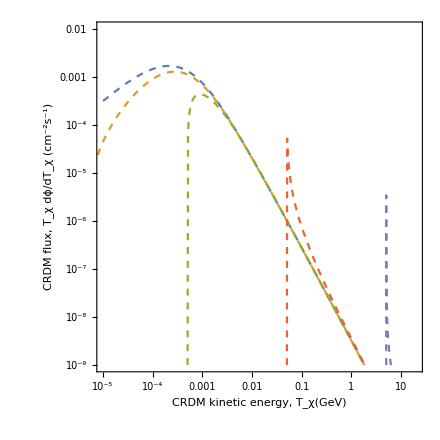
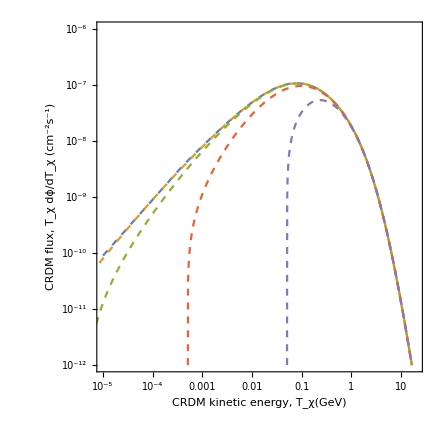

```mathematica
inelasFluxPlot1MeVlight=ListLogLogPlot[
Join[{datFluxVecElas⟦1⟧},datFluxVecM1MeVlight],PlotStyle->Dashed,
commonOptions];
inelasFluxPlot100MeVheavy=ListLogLogPlot[
Join[{datFluxVecElas[[2]]},datFluxVecM100MeVheavy],PlotStyle->Dashed,
PlotRange->{{10^-5,20},{10^-12,10^-6}},commonOptions];
{inelasFluxPlot1MeVlight,inelasFluxPlot100MeVheavy}
```

## DM decay

This section describes the decay of the upscattered χ_2 particles to χ_1+ γ and calculates the resulting χ_1 and γ spectra

### Kinematics

CoM decay kinematics with 1 massless particle:

Px == px' + pγ

Ei == M + Tx

Ex==(M^2+mx^2)/(2M)
Eγ==(M^2-mx^2)/(2M)

pxCoM==(√((M^2+mx^2)^2-4 M^2 mx^2))/(2M)==(M^2-mx^2)/(2M)
pγCoM==Eγ==(M^2-mx^2)/(2M)

Take M = mx + δ and break into components, along and perpendicular to the parent particle’s direction:

pxCoMi==((mx+δ)^2-mx^2)/(2(mx+δ))Sinθd
pxCoMj==((mx+δ)^2-mx^2)/(2(mx+δ))Cosθd

pγCoMi==-((mx+δ)^2-mx^2)/(2(mx+δ))Sinθd
pγCoMj==-((mx+δ)^2-mx^2)/(2(mx+δ))Cosθd

Boosting, γ = Ei/M:

pxi==(δ (2 mx+δ))/(2 (mx+δ))Sinθd
pxj==γ((δ (2 mx+δ))/(2 (mx+δ))Cosθd+β[γ]Ex)==(mx+δ+Tx)/(mx+δ)((δ (2 mx+δ))/(2 (mx+δ))Cosθd+β[(mx+δ+Tx)/(mx+δ)]((mx+δ)^2+mx^2)/(2(mx+δ)))

TxB=√(px^2+mx^2)-mx==√(pxi^2+pxj^2+mx^2)-mx

Define energy of outgoing DM after decay:

```mathematica
β[γ_]:=(1-γ^-2)^(1/2)
```

```mathematica
Tx1[Tx2_,mx1_,δ_,cosθd_]=
√((δ^2 (2 mx1+δ)^2)/(4(mx1+δ)^2)Sin[ArcCos[cosθd]]^2+((mx1+δ+Tx2)/(mx1+δ)((δ (2 mx1+δ))/(2 (mx1+δ))cosθd+β[(mx1+δ+Tx2)/(mx1+δ)]((mx1+δ)^2+mx1^2)/(2(mx1+δ))))^2+mx1^2)-mx1//Simplify
```

-mx1+√(mx1^2-((-1+cosθd^2) δ^2 (2 mx1+δ)^2)/(4 (mx1+δ)^2)+((mx1+Tx2+δ)^2 (cosθd δ (2 mx1+δ)+√((Tx2 (2 mx1+Tx2+2 δ))/(mx1+Tx2+δ)^2) (mx1^2+(mx1+δ)^2))^2)/(4 (mx1+δ)^4))

Different colors are different δ

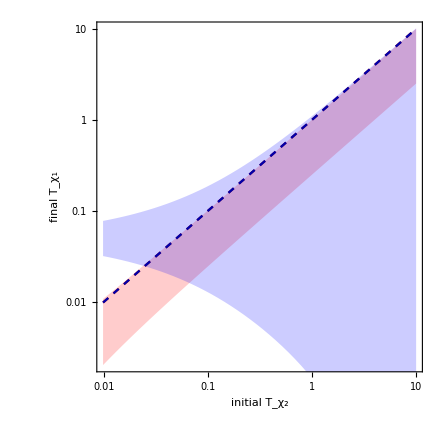
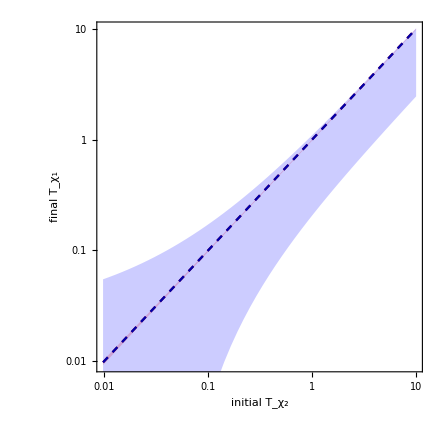

```mathematica
{Show[
LogLogPlot[{TX,Tx1[TX,.001,.001,-1],Tx1[TX,.001,.001,1]},{TX,0,10},PlotStyle->{{Dashed,Red//Darker},None,None},Filling->2->{3},FillingStyle->Opacity[.2,Red],FrameLabel->{"initial T_χ_2","final T_χ_1"}],
LogLogPlot[{TX,Tx1[TX,.001,.1,-1],Tx1[TX,.001,.1,1]},{TX,0,10},PlotStyle->{{Dashed,Blue//Darker},None,None},Filling->2->{3},FillingStyle->Opacity[.2,Blue]]],
Show[
LogLogPlot[{TX,Tx1[TX,.1,.001,-1],Tx1[TX,.1,.001,1]},{TX,0,10},PlotStyle->{{Dashed,Red//Darker},None,None},Filling->2->{3},FillingStyle->Opacity[.2,Red],FrameLabel->{"initial T_χ_2","final T_χ_1"}],
LogLogPlot[{TX,Tx1[TX,.1,.1,-1],Tx1[TX,.1,.1,1]},{TX,0,10},PlotStyle->{{Dashed,Blue//Darker},None,None},Filling->2->{3},FillingStyle->Opacity[.2,Blue]]]}
```

```mathematica
Solve[TXb==γ(mx+δ^2/(2 (mx+δ)))+γ β[γ] √(2 mx δ^2/(2 (mx+δ))+(δ^2/(2 (mx+δ)))^2) cosθ-mx/.γ->(mx+δ+Tx)/(mx+δ),Tx]//FullSimplify
```

{{Tx→(cosθ^2 δ^2 (mx+δ) (2 mx+δ)^2+(mx+δ) (2 mx TXb+(2 TXb-δ) δ) (2 mx^2+2 mx δ+δ^2)+√(cosθ^2 δ^2 (mx+δ)^2 (2 mx+δ)^2 (4 mx^2 TXb (2 mx+TXb)+8 mx TXb (2 mx+TXb) δ+4 ((-1+cosθ^2) mx^2+2 mx TXb+TXb^2) δ^2+4 (-1+cosθ^2) mx δ^3+(-1+cosθ^2) δ^4)))/((2 mx^2-2 (-1+cosθ) mx δ-(-1+cosθ) δ^2) (2 mx^2+2 (1+cosθ) mx δ+(1+cosθ) δ^2))},{Tx→(cosθ^2 δ^2 (mx+δ) (2 mx+δ)^2+(mx+δ) (2 mx TXb+(2 TXb-δ) δ) (2 mx^2+2 mx δ+δ^2)-√(cosθ^2 δ^2 (mx+δ)^2 (2 mx+δ)^2 (4 mx^2 TXb (2 mx+TXb)+8 mx TXb (2 mx+TXb) δ+4 ((-1+cosθ^2) mx^2+2 mx TXb+TXb^2) δ^2+4 (-1+cosθ^2) mx δ^3+(-1+cosθ^2) δ^4)))/((2 mx^2-2 (-1+cosθ) mx δ-(-1+cosθ) δ^2) (2 mx^2+2 (1+cosθ) mx δ+(1+cosθ) δ^2))}}

Initial Tx2 (in lab frame) to achieve a given boosted Tx1:

```mathematica
Tx2[Tx1_,mx1_,δ_,cosθ_]:=
(cosθ^2 δ^2 (mx1+δ) (2 mx1+δ)^2+(mx1+δ) (2 mx1 Tx1+(2 Tx1-δ) δ) (2 mx1^2+2 mx1 δ+δ^2)-√(cosθ^2 δ^2 (mx1+δ)^2 (2 mx1+δ)^2 (4 mx1^2 Tx1 (2 mx1+Tx1)+8 mx1 Tx1 (2 mx1+Tx1) δ+4 ((-1+cosθ^2) mx1^2+2 mx1 Tx1+Tx1^2) δ^2+4 (-1+cosθ^2) mx1 δ^3+(-1+cosθ^2) δ^4)))/((2 mx1^2-2 (-1+cosθ) mx1 δ-(-1+cosθ) δ^2) (2 mx1^2+2 (1+cosθ) mx1 δ+(1+cosθ) δ^2))
```

Minimum/maximum initial energy Tx2 that can be boosted to a final Tx1:

```mathematica
Solve[Tx1[TX2,mx1,δ,1]==TX1,TX2]//FullSimplify
```

{{TX2→-(mx1 (2 mx1+δ)^2+√(TX1 (2 mx1+TX1) δ^2 (2 mx1+δ)^2)+TX1 (2 mx1^2+2 mx1 δ+δ^2))/(2 mx1^2)},{TX2→(2 mx1^2 TX1+2 mx1 TX1 δ+(mx1+TX1) δ^2-√(TX1 (2 mx1+TX1) δ^2 (2 mx1+δ)^2))/(2 mx1^2)},{TX2→(-mx1 (2 mx1+δ)^2+√(TX1 (2 mx1+TX1) δ^2 (2 mx1+δ)^2)-TX1 (2 mx1^2+2 mx1 δ+δ^2))/(2 mx1^2)},{TX2→(2 mx1^2 TX1+2 mx1 TX1 δ+(mx1+TX1) δ^2+√(TX1 (2 mx1+TX1) δ^2 (2 mx1+δ)^2))/(2 mx1^2)}}

```mathematica
Tx2min[Tx1_,mx_,δ_]:=(2 mx^2 Tx1+2 mx Tx1 δ+(mx+Tx1) δ^2-√(Tx1 (2 mx+Tx1) δ^2 (2 mx+δ)^2))/(2 mx^2)
Tx2max[Tx1_,mx_,δ_]:=(2 mx^2 Tx1+2 mx Tx1 δ+(mx+Tx1) δ^2+√(Tx1 (2 mx+Tx1) δ^2 (2 mx+δ)^2))/(2 mx^2)
```

### Decay photon

Energy of photon in detector frame:

```mathematica
Eγb[Tx_,mx_,δ_,cosθ_]:=γ (δ (2 mx+δ))/(2 (mx+δ))(1-β[γ]cosθ)/.γ->(mx+δ+Tx)/(mx+δ)
```

Minimum Tx to give Eγ in detector frame:

```mathematica
Solve[Eγb[Tx,mx,δ,-1]==Eγ,Tx]//FullSimplify
```

{{Tx→(-2 Eγ (mx+δ)+δ (2 mx+δ))^2/(4 Eγ δ (2 mx+δ))}}

```mathematica
TxMinEγ[Eγ_?NumericQ,mx_?NumericQ,δ_?NumericQ]:=(-2 Eγ (mx+δ)+δ (2 mx+δ))^2/(4 Eγ δ (2 mx+δ))
```

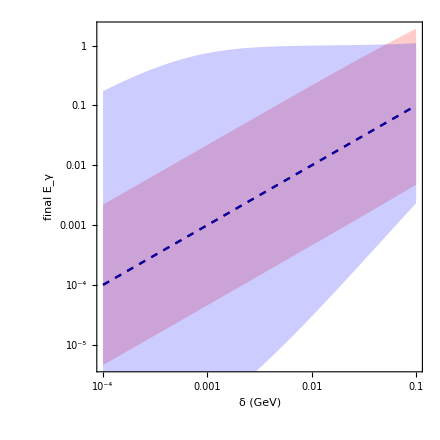

```mathematica
Show[LogLogPlot[{δ,Eγb[10,1,δ,-1],Eγb[10,1,δ,1]},{δ,.0001,.1},PlotStyle->{{Dashed,Red//Darker},None,None},Filling->2->{3},FillingStyle->Opacity[.2,Red],FrameLabel->{"δ (GeV)","final E_γ"}],
LogLogPlot[{δ,Eγb[1,.001,δ,-1],Eγb[1,.001,δ,1]},{δ,.0001,.1},PlotStyle->{{Dashed,Blue//Darker},None,None},Filling->2->{3},FillingStyle->Opacity[.2,Blue]]]
```

### Define post decay flux

Function for the upscattered χ_1dark matter flux after decay from χ_2, contributions from protons and helium included.
	Tx1 = flux is computed for the χ_1DM kinetic energy Tx1
	mx = mass of dark matter
	δ = mass splitting
	gxi = to mediator coupling (takes x and nucleon coupling as the same)
	mA = mass of mediator
Units of returned flux are GeV^2

```mathematica
dϕX1dTx1[TX1_?NumericQ,mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,mA_?NumericQ]:=
Deff*(ρX/(mx GeV))(
If[(TX1<Tx1[TxMin[TdatMax⟦1⟧,mi⟦1⟧,mx,δ],mx,δ,-1] ∨ TiMinGlobal[mi⟦1⟧,mx,δ]>TdatMax⟦1⟧),10^-100,
NIntegrate[
pFlux[Tii]dσidTxVector[TX2,Tii,mx,δ,gxi,mA,1]((δ (2 mx+δ) √(TX2 (2 mx+TX2+2 δ)))/(mx+δ)^2)^-1 GeV,
{TX2,Tx2min[TX1,mx,δ],Tx2max[TX1,mx,δ]},
{Tii,Max[TdatMin⟦1⟧,Min[TiMin[TX2,mi⟦1⟧,mx,δ],TdatMax⟦1⟧]],TdatMax⟦1⟧},AccuracyGoal->∞,Method->{"GlobalAdaptive"},PrecisionGoal->3]
]
+If[(TX1<Tx1[TxMin[TdatMax⟦2⟧,mi⟦2⟧,mx,δ],mx,δ,-1] ∨ TiMinGlobal[mi⟦2⟧,mx,δ]>TdatMax⟦2⟧),10^-100,
NIntegrate[
heFlux[Tii]dσidTxVector[TX2,Tii,mx,δ,gxi,mA,2]((δ (2 mx+δ) √(TX2 (2 mx+TX2+2 δ)))/(mx+δ)^2)^-1 GeV,
{TX2,Tx2min[TX1,mx,δ],Tx2max[TX1,mx,δ]},
{Tii,Max[TdatMin⟦2⟧,Min[TiMin[TX2,mi⟦2⟧,mx,δ],TdatMax⟦2⟧]],TdatMax⟦2⟧},AccuracyGoal->∞,Method->{"GlobalAdaptive"},PrecisionGoal->3]
])
```

Photon flux:
	variables are same as above except Eγ is the photon energy in GeV

```mathematica
dϕγdE[Eγ_?NumericQ,mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,mϕ_?NumericQ]:=
If[Eγ>Eγb[10,mx,δ,-1]∨Eγ<Eγb[10,mx,δ,1],0,
(((mx+δ)^2-mx^2)/(2(mx+δ)))^-1 Deff*(ρX/(mx GeV))
Sum[
NIntegrate[
dϕdT[Tii,ii]dσidTxVector[TX,Tii,mx,δ,gxi,mϕ,ii]((2 √((TX+mx+δ)^2-(mx+δ)^2))/(mx+δ))^-1 GeV,
{TX,TxMinEγ[Eγ,mx,δ],100},
{Tii,Min[TiMin[100,mi⟦ii⟧,mx,δ],TdatMax⟦ii⟧],TdatMax⟦ii⟧},AccuracyGoal->∞,PrecisionGoal->3]
,{ii,1,2}]]
```

Define function which returns of list of samples of the χ_1 spectra after decay
	variable are same as above, but with the flux returned for nPoints (log sampled) between {TX1MIN, TX1MAX}

```mathematica
dϕX1dTx1list[TX1MIN_?NumericQ,TX1MAX_?NumericQ,mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,mA_?NumericQ,nPoints_?NumericQ]:=
Module[{fluxX2,Tx2Points,maxF},
fluxX2=dϕX2dTx2list[Tx2min[TX1MIN,mx,δ],Min[Tx2max[TX1MAX,mx,δ],1000],mx,δ,gxi,mA,2nPoints]//Interpolation[#,InterpolationOrder->1]&;
ParallelTable[
{TX1, If[(TX1<Tx1[fluxX2⟦1,1,1⟧,mx,δ,-1]),10^-100,
 NIntegrate[
  fluxX2[TX2]((δ (2 mx+δ)√(TX2(2 mx+TX2+2 δ)))/(mx+δ)^2)^-1,
  {TX2,Min[Max[Tx2min[TX1,mx,δ],fluxX2⟦1,1,1⟧],Tx2max[TX1,mx,δ]],Min[fluxX2⟦1,1,2⟧,Tx2max[TX1,mx,δ]]},
  AccuracyGoal->∞,PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]]}
,{TX1,logSpace[TX1MIN,TX1MAX,nPoints]}]//Return
];
```

Define function which returns of list of samples of the γ spectra
	variable are same as above, but with the flux returned for nPoints (log sampled) between {EMIN, EMAX}

```mathematica
dϕγdElist[EMIN_?NumericQ,EMAX_?NumericQ,mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,mA_?NumericQ,nPoints_?NumericQ]:=
Module[{fluxX2,TxPoints},
fluxX2=
dϕX2dTx2list[1.00001TxMin[TdatMax⟦1⟧,mi⟦1⟧,mx,δ],Min[TxMax[TdatMax⟦1⟧,mi⟦1⟧,mx,δ],1000],mx,δ,gxi,mA,Max[2nPoints,60]]
//Interpolation[#,InterpolationOrder->1]&;
ParallelTable[{Eγ,
(((mx+δ)^2-mx^2)/(2(mx+δ)))^-1 GeV^2
NIntegrate[
  fluxX2[TX]((2 √((TX+mx+δ)^2-(mx+δ)^2))/(mx+δ))^-1,
  {TX,Max[fluxX2⟦1,1,1⟧,TxMinEγ[Eγ,mx,δ]],Max[TxMinEγ[Eγ,mx,δ],fluxX2[[1,1,2]]]},
   AccuracyGoal->∞,PrecisionGoal->3]},
{Eγ,logSpace[EMIN,EMAX,nPoints]}]//Return
];
```

### Calculate fluxes

#### CRDM flux

```mathematica
With[{MX=.001,MA=.001,nPoints=200},
datDecayDMfluxM1MeVδp1MeV=dϕX1dTx1list[10^-5,10,MX,.0001,gxLight,MA,nPoints];
datDecayDMfluxM1MeVδp1MeV[[All,2]]*=datDecayDMfluxM1MeVδ1MeV[[All,1]]unitsCM2S GeV^3 cm^2 s;

datDecayDMfluxM1MeVδ1MeV=dϕX1dTx1list[10^-5,10,MX,.001,gxLight,MA,nPoints];
datDecayDMfluxM1MeVδ1MeV[[All,2]]*=datDecayDMfluxM1MeVδ1MeV[[All,1]]unitsCM2S GeV^3 cm^2 s;

datDecayDMfluxM1MeVδ10MeV=dϕX1dTx1list[10^-5,10,MX,.01,gxLight,MA,nPoints];
datDecayDMfluxM1MeVδ10MeV[[All,2]]*=datDecayDMfluxM1MeVδ10MeV[[All,1]]unitsCM2S GeV^3 cm^2 s;

datDecayDMfluxM1MeVδ100MeV=dϕX1dTx1list[.01,10,MX,.1,gxLight,MA,2 nPoints];
datDecayDMfluxM1MeVδ100MeV[[All,2]]*=datDecayDMfluxM1MeVδ100MeV[[All,1]]unitsCM2S GeV^3 cm^2 s;
]
```

```mathematica
With[{MX=.1,MA=1,nPoints=200},
datDecayDMfluxM100MeVδp1MeV=dϕX1dTx1list[10^-5,20,MX,.0001,gxHeavy,MA,nPoints];
datDecayDMfluxM100MeVδp1MeV[[All,2]]*=datDecayDMfluxM100MeVδ1MeV[[All,1]]unitsCM2S GeV^3 cm^2 s;

datDecayDMfluxM100MeVδ1MeV=dϕX1dTx1list[10^-5,20,MX,.001,gxHeavy,MA,nPoints];
datDecayDMfluxM100MeVδ1MeV[[All,2]]*=datDecayDMfluxM100MeVδ1MeV[[All,1]]unitsCM2S GeV^3 cm^2 s;

datDecayDMfluxM100MeVδ10MeV=dϕX1dTx1list[10^-5,20,MX,.01,gxHeavy,MA,nPoints];
datDecayDMfluxM100MeVδ10MeV[[All,2]]*=datDecayDMfluxM100MeVδ10MeV[[All,1]]unitsCM2S GeV^3 cm^2 s;

datDecayDMfluxM100MeVδ100MeV=dϕX1dTx1list[10^-4,20,MX,.1,gxHeavy,MA,nPoints];
datDecayDMfluxM100MeVδ100MeV[[All,2]]*=datDecayDMfluxM100MeVδ100MeV[[All,1]]unitsCM2S GeV^3 cm^2 s;
]
```

#### Photon flux

```mathematica
datDecayγFluxM1MeV=
With[{MX=.001,MA=.001,EMIN=10^-3,EMAX=10,nPoints=200},

{dϕγdElist[EMIN,EMAX,MX,0.0001,gxLight,MA,nPoints],
dϕγdElist[EMIN,EMAX,MX,0.001,gxLight,MA,nPoints],
 dϕγdElist[EMIN,EMAX,MX,0.010,gxLight,MA,nPoints],
 dϕγdElist[EMIN,EMAX,MX,0.100,gxLight,MA,2 nPoints]}];
```

```mathematica
datDecayγFluxM100MeV=
With[{MX=.1,MA=1,EMIN=10^-3,EMAX=10,nPoints=200},

{dϕγdElist[EMIN,EMAX,MX,0.0001,gxHeavy,MA,nPoints],
dϕγdElist[EMIN,EMAX,MX,0.001,gxHeavy,MA,nPoints],
 dϕγdElist[EMIN,EMAX,MX,0.010,gxHeavy,MA,nPoints],
 dϕγdElist[EMIN,EMAX,MX,0.100,gxHeavy,MA,nPoints]}];
```

Fraction of flux from b>30^o is ~0.19 (see CR notebook), however IGRB is 80% accounted for, so can approximate limit based on equating total decay γ flux to the total IGRB flux. 
Convert units to those used by Fermi data (GeV/cm^2/s/sr):

```mathematica
Do[datDecayγFluxM1MeV⟦ii,All,2⟧ *= 1/(4π)GeV (unitsCM2S cm^2 s) datDecayγFluxM1MeV⟦ii,All,1⟧^2,{ii,1,4}];
```

```mathematica
Do[datDecayγFluxM100MeV⟦ii,All,2⟧ *= 1/(4π)GeV (unitsCM2S cm^2 s) datDecayγFluxM100MeV⟦ii,All,1⟧^2,{ii,1,4}];
```

### Dark matter flux plots

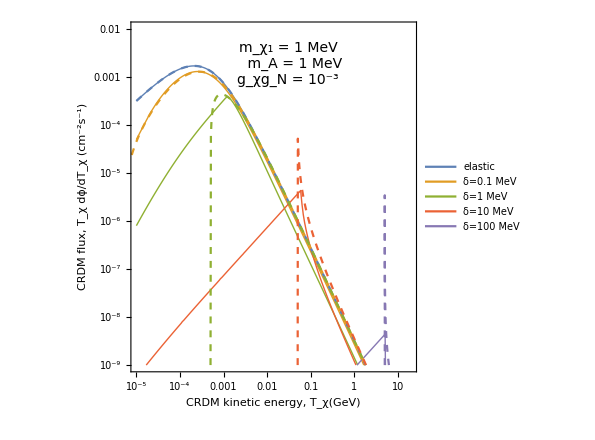

```mathematica
fluxPlot1MeVlight=Show[
ListLogLogPlot[{datFluxVecElas⟦1⟧,datDecayDMfluxM1MeVδp1MeV,datDecayDMfluxM1MeVδ1MeV,datDecayDMfluxM1MeVδ10MeV,datDecayDMfluxM1MeVδ100MeV},
Joined->True,commonOptions,
Epilog->Inset[Style[" m_χ_1 = 1 MeV\n   m_A = 1 MeV\ng_χg_N = 10^-3     ",14,FontFamily->"Times"],Scaled[{.55,.88}]],
PlotLegends->Legend[{"elastic","δ=0.1 MeV","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.85,.84}]],
inelasFluxPlot1MeVlight]
```

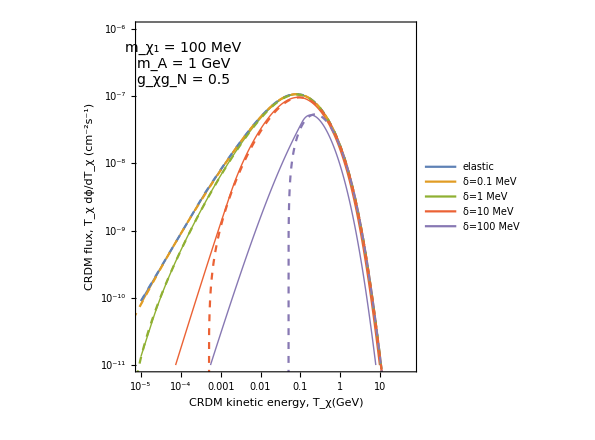

```mathematica
fluxPlot100MeVheavy=Show[
ListLogLogPlot[{datFluxVecElas⟦2⟧,datDecayDMfluxM100MeVδp1MeV,datDecayDMfluxM100MeVδ1MeV,datDecayDMfluxM100MeVδ10MeV,datDecayDMfluxM100MeVδ100MeV},
Joined->True,PlotRange->{{10^-5,60},{10^-11,10^-6}},commonOptions,
Epilog->Inset[Style["   m_χ_1 = 100 MeV\nm_A = 1 GeV\ng_χg_N = 0.5         ",14,FontFamily->"Times"],Scaled[{.17,.88}]],
PlotLegends->Legend[{"elastic","δ=0.1 MeV","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.85,.84}]],
inelasFluxPlot100MeVheavy
]
```

```mathematica
Export["figures/fig_flux_1MeV.pdf",fluxPlot1MeVlight];
Export["figures/fig_flux_100MeV.pdf",fluxPlot100MeVheavy];
```

### Photon flux plot

Import Fermi data from fig.5 of 1501.05464:

```mathematica
fermiIGRB=Import["data/FERMI_IGRB.csv"];
```

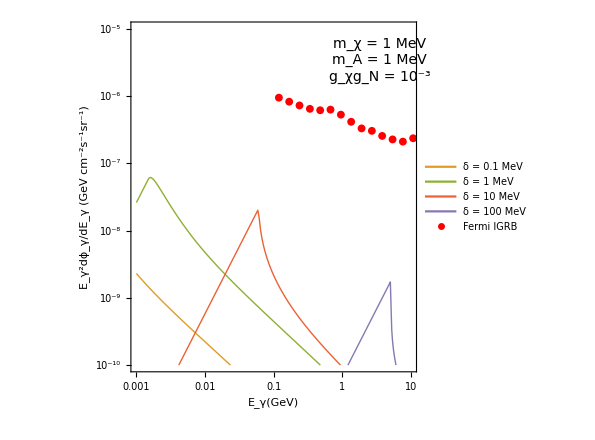
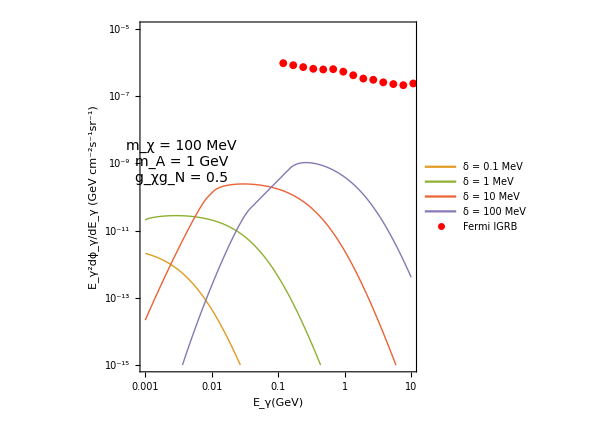

```mathematica
{photonFluxPlot1MeV=Show[ListLogLogPlot[datDecayγFluxM1MeV,
Joined->True,FrameTicks->{LogTicks[10^-15,.1],LogTicks[10^-6,10^3]},
PlotRange->{{10^-3,10},{10^-10,10^-5}},PlotLegends->Legend[{"δ = 0.1 MeV","δ = 1 MeV","δ = 10 MeV","δ = 100 MeV"},Position->{.18,.86}],
FrameLabel->{"E_γ(GeV)","E_γ^2dϕ_γ/dE_γ (GeV cm^-2s^-1sr^-1)"},
PlotStyle->({#,Thick}&/@ColorData[97,"ColorList"][[{2,3,4,5}]]),
Epilog->Inset[Style["m_χ = 1 MeV\nm_A = 1 MeV\ng_χg_N = 10^-3",14,FontFamily->"Times"],Scaled[{.87,.89}]]]
,
ListLogLogPlot[fermiIGRB,PlotStyle->Red,PlotLegends->Legend[{"Fermi IGRB"},Position->{.18,.7}]]],
photonFluxPlot100MeV=Show[ListLogLogPlot[datDecayγFluxM100MeV,
Joined->True,FrameTicks->{LogTicks[10^-15,.1],LogTicks[10^-6,10^3]},
PlotRange->{{10^-3,10},{10^-15,10^-5}},PlotLegends->Legend[{"δ = 0.1 MeV","δ = 1 MeV","δ = 10 MeV","δ = 100 MeV"},Position->{.18,.86}],
PlotStyle->({#,Thick}&/@ColorData[97,"ColorList"][[{2,3,4,5}]]),
FrameLabel->{"E_γ(GeV)","E_γ^2dϕ_γ/dE_γ (GeV cm^-2s^-1sr^-1)"},
Epilog->Inset[Style["     m_χ = 100 MeV\nm_A = 1 GeV\ng_χg_N = 0.5",14,FontFamily->"Times"],Scaled[{.15,.6}]]]
,
ListLogLogPlot[fermiIGRB,PlotStyle->Red,PlotLegends->Legend[{"Fermi IGRB"},Position->{.18,.72}]]]}
```

```mathematica
Export["./figures/fig_photon_flux_m1MeV.pdf",photonFluxPlot1MeV];
Export["./figures/fig_photon_flux_m100MeV.pdf",photonFluxPlot100MeV];
```

## CRiDM scattering on Earth

This section describes the scattering of the upscattered dark matter component in a detector on Earth.

Two scenarios are considered:
I. χ_1 (produced from decay of χ_2) endothermically scatters in the detector
II. χ_2 lives long enough to exothermically scatter in the detector

### Kinematics for up-scatter

Find minimum Tx to produce an upscatter with energy Er:

3-momentum conservation:
p(mx+δ) = p’(mx) + k(mT)
re-arrange and squaring:
(p')^2 = (p - k)^2

```mathematica
Solve[((Txp+mxp)^2-(mxp)^2)==((Tx+mx)^2-mx^2)+((Er+mT)^2-mT^2)+2 √(((Tx+mx)^2-mx^2)((Er+mT)^2-mT^2))/.{mxp->mx+δ,Txp->Tx-Er-δ},{Tx}]//FullSimplify
```

{{Tx→(Er (2 Er mT-4 mT mx+δ (2 mx+δ))-√(Er (Er+2 mT) (2 Er mT+δ^2) (2 Er mT+(2 mx+δ)^2)))/(4 Er mT)},{Tx→(Er (2 Er mT-4 mT mx+δ (2 mx+δ))+√(Er (Er+2 mT) (2 Er mT+δ^2) (2 Er mT+(2 mx+δ)^2)))/(4 Er mT)}}

Define functions for kinematic limits
	Er = recoil energy
	mT = target nuclei mass

```mathematica
TxMinEu[Er_?NumericQ,mT_?NumericQ,mx_?NumericQ,δ_?NumericQ]:=
1/(4 Er mT)(Er (2 Er mT-4 mT mx+δ (2 mx+δ))+√(Er (Er+2 mT) (2 Er mT+δ^2) (2 Er mT+(2 mx+δ)^2)))
```

Global min:

```mathematica
TxMinU[mT_,mx_,δ_]=1/(4 Er mT)(Er (2 Er mT-4 mT mx+δ (2 mx+δ))+√(Er (Er+2 mT) (2 Er mT+δ^2) (2 Er mT+(2 mx+δ)^2)))/.Er->(2 mx δ+δ^2)/(2 (mT+mx+δ))//FullSimplify;
```

Find the kinematic limits on the recoil energy:

```mathematica
Solve[((Txp+mxp)^2-(mxp)^2)==((Tx+mx)^2-mx^2)+((Er+mT)^2-mT^2)+2 √(((Tx+mx)^2-mx^2)((Er+mT)^2-mT^2))/.{mxp->mx+δ,Txp->Tx-Er-δ},{Er}]//FullSimplify
```

{{Er→-1/(2 (mT+mx)^2+4 mT Tx)(-2 mT Tx (2 mx+Tx)+2 mx (mT+mx+Tx) δ+(mT+mx+Tx) δ^2+√(Tx (2 mx+Tx) (2 mT Tx-2 (mT+mx) δ-δ^2) (-δ (2 mx+δ)+2 mT (2 mx+Tx+δ))))},{Er→1/(2 (mT+mx)^2+4 mT Tx)(2 mT Tx (2 mx+Tx)-2 mx (mT+mx+Tx) δ-(mT+mx+Tx) δ^2+√(Tx (2 mx+Tx) (2 mT Tx-2 (mT+mx) δ-δ^2) (-δ (2 mx+δ)+2 mT (2 mx+Tx+δ))))}}

Define functions for the kinematic limits:

```mathematica
ErMinU[Tx_?NumericQ,mx_?NumericQ,δ_?NumericQ,mT_?NumericQ]:=
If[-mT-mx+√(mT^2+2 mT mx+mx^2+2 mT Tx)<δ,0,
-1/(2 (mT+mx)^2+4 mT Tx)(-2 mT Tx (2 mx+Tx)+2 mx (mT+mx+Tx) δ+(mT+mx+Tx) δ^2+√(Tx (2 mx+Tx) (2 mT Tx-2 (mT+mx) δ-δ^2) (-δ (2 mx+δ)+2 mT (2 mx+Tx+δ))))]
```

```mathematica
ErMaxU[Tx_?NumericQ,mx_?NumericQ,δ_?NumericQ,mT_?NumericQ]:=
If[-mT-mx+√(mT^2+2 mT mx+mx^2+2 mT Tx)<δ,0,
1/(2 (mT+mx)^2+4 mT Tx)(2 mT Tx (2 mx+Tx)-2 mx (mT+mx+Tx) δ-(mT+mx+Tx) δ^2+√(Tx (2 mx+Tx) (2 mT Tx-2 (mT+mx) δ-δ^2) (-δ (2 mx+δ)+2 mT (2 mx+Tx+δ))))]
```

### Kinematics for down-scatter

Excited DM comes in with kinetic energy = Tx and  mass = mx’ = mx + δ, de-excited goes out

3-momentum conservation:
p(mx+δ) = p’(mx) + k(mT)
re-arrange and squaring:
(p')^2 = (p - k)^2

Find minimum Tx to produce a downscatter with recoil energy Er:

```mathematica
Solve[((Txp+mxp)^2-mxp^2)==((Tx+mxi)^2-mxi^2)+((Er+mT)^2-mT^2)+2 √(((Tx+mxi)^2-mxi^2)((Er+mT)^2-mT^2))/.{mxp->mx,mxi->mx+δ,Txp->Tx-Er+δ},{Tx}]//FullSimplify
```

{{Tx→(Er (2 Er mT-4 mT (mx+δ)-δ (2 mx+δ))-√(Er (Er+2 mT) (2 Er mT+δ^2) (2 Er mT+(2 mx+δ)^2)))/(4 Er mT)},{Tx→(Er (2 Er mT-4 mT (mx+δ)-δ (2 mx+δ))+√(Er (Er+2 mT) (2 Er mT+δ^2) (2 Er mT+(2 mx+δ)^2)))/(4 Er mT)}}

```mathematica
TxMinEd[Er_?NumericQ,mT_?NumericQ,mx_?NumericQ,δ_?NumericQ]:=
(Er (2 Er mT-4 mT (mx+δ)-δ (2 mx+δ))+√(Er (Er+2 mT) (2 Er mT+δ^2) (2 Er mT+(2 mx+δ)^2)))/(4 Er mT)
```

Find the kinematic limits on the recoil energy:

```mathematica
Solve[((Txp+mxp)^2-(mxp)^2)==((Tx+mxi)^2-mxi^2)+((Er+mT)^2-mT^2)+2 √(((Tx+mxi)^2-mxi^2)((Er+mT)^2-mT^2))/.{Txp->Tx-Er+δ,mxp->mx,mxi->mx+δ},{Er}]
```

{{Er→1/(2 (4 mT^2+8 mT mx+4 mx^2+8 mT Tx+8 mT δ+8 mx δ+4 δ^2))(16 mT mx Tx+8 mT Tx^2+8 mT mx δ+8 mx^2 δ+16 mT Tx δ+8 mx Tx δ+4 mT δ^2+12 mx δ^2+4 Tx δ^2+4 δ^3-√(4 δ^2 (-4 mx^2-4 mx δ-δ^2) (4 mT^2+8 mT mx+4 mx^2+8 mT Tx+8 mT δ+8 mx δ+4 δ^2)+(-16 mT mx Tx-8 mT Tx^2-8 mT mx δ-8 mx^2 δ-16 mT Tx δ-8 mx Tx δ-4 mT δ^2-12 mx δ^2-4 Tx δ^2-4 δ^3)^2))},{Er→1/(2 (4 mT^2+8 mT mx+4 mx^2+8 mT Tx+8 mT δ+8 mx δ+4 δ^2))(16 mT mx Tx+8 mT Tx^2+8 mT mx δ+8 mx^2 δ+16 mT Tx δ+8 mx Tx δ+4 mT δ^2+12 mx δ^2+4 Tx δ^2+4 δ^3+√(4 δ^2 (-4 mx^2-4 mx δ-δ^2) (4 mT^2+8 mT mx+4 mx^2+8 mT Tx+8 mT δ+8 mx δ+4 δ^2)+(-16 mT mx Tx-8 mT Tx^2-8 mT mx δ-8 mx^2 δ-16 mT Tx δ-8 mx Tx δ-4 mT δ^2-12 mx δ^2-4 Tx δ^2-4 δ^3)^2))}}

Define functions for the kinematic limits:

```mathematica
ErMinD[Tx_?NumericQ,mx_?NumericQ,δ_?NumericQ,mT_?NumericQ]:=
1/(2 (4 mT^2+8 mT mx+4 mx^2+8 mT Tx+8 mT δ+8 mx δ+4 δ^2))(16 mT mx Tx+8 mT Tx^2+8 mT mx δ+8 mx^2 δ+16 mT Tx δ+8 mx Tx δ+4 mT δ^2+12 mx δ^2+4 Tx δ^2+4 δ^3-√(4 δ^2 (-4 mx^2-4 mx δ-δ^2) (4 mT^2+8 mT mx+4 mx^2+8 mT Tx+8 mT δ+8 mx δ+4 δ^2)+(-16 mT mx Tx-8 mT Tx^2-8 mT mx δ-8 mx^2 δ-16 mT Tx δ-8 mx Tx δ-4 mT δ^2-12 mx δ^2-4 Tx δ^2-4 δ^3)^2))
```

```mathematica
ErMaxD[Tx_?NumericQ,mx_?NumericQ,δ_?NumericQ,mT_?NumericQ]:=
1/(2 (4 mT^2+8 mT mx+4 mx^2+8 mT Tx+8 mT δ+8 mx δ+4 δ^2))(16 mT mx Tx+8 mT Tx^2+8 mT mx δ+8 mx^2 δ+16 mT Tx δ+8 mx Tx δ+4 mT δ^2+12 mx δ^2+4 Tx δ^2+4 δ^3+√(4 δ^2 (-4 mx^2-4 mx δ-δ^2) (4 mT^2+8 mT mx+4 mx^2+8 mT Tx+8 mT δ+8 mx δ+4 δ^2)+(-16 mT mx Tx-8 mT Tx^2-8 mT mx δ-8 mx^2 δ-16 mT Tx δ-8 mx Tx δ-4 mT δ^2-12 mx δ^2-4 Tx δ^2-4 δ^3)^2))
```

These match with equation 11 of 2006.14089, but since we are scattering from a nucleus and not an electron, we don’t have a sharp peak in recoil energy.

### Define cross sections

#### Upscatter

Differential cross section for the endothermic scatter of χ_1 on a nuclear target with A nucleons
	Er = recoil energy
	Tx1 = incoming χ_1 kinetic energy
	returned cross section has units GeV^-3

```mathematica
dσdErUp[Er_?NumericQ,Tx1_?NumericQ,A_?NumericQ,mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,mA_?NumericQ]:=
(gxi^4/(2π GeV^4) A^2 Fhelm[√(2 A amu Er),A]^2)(2(A amu)Er^2-Er(2(A amu+mx)^2+4 A amu Tx1+4mx δ +δ^2)+(A amu)(4(mx+Tx1)^2-δ^2))GeV/((mA^2+2(A amu) Er)^2(Tx1^2+2mx Tx1))
```

#### Downscatter

Differential cross section for the exothermic scatter of χ_2 on a nuclear target with A nucleons
	Er = recoil energy
	Tx2 = incoming χ_2 kinetic energy
	returned cross section has units GeV^-3

```mathematica
dσdErDown[Er_?NumericQ,Tx2_?NumericQ,A_?NumericQ,mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,mA_?NumericQ]:=
(gxi^4/(2π GeV^4) A^2 Fhelm[√(2 A amu Er),A]^2)(2 (A amu)Er^2-Er(2(A amu+mx)^2+4 A amu Tx2+4(A amu)δ-δ^2)+(A amu) (4 (mx+Tx2)^2+6 (mx+Tx2)δ+δ^2))GeV/((mA^2+2(A mp) Er)^2(Tx2^2+2(mx+δ) Tx2))
```

### Define differential rates for xenon

Here we consider scattering on xenon, which we treat as a single isotope: xenon-131

```mathematica
(*Energies above this are assumed to be attenuated*)
TXMAX=10^2;
```

Define functions that return a list of { Er (keV) , rate (/tonne/yr/keV)}, sampled from ErMinGeV to ErMaxGeV with nPoints (log spaced)

```mathematica
dRdErUpList[ERMIN_?NumericQ,ERMAX_?NumericQ,mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,MA_?NumericQ,nPoints_:30]:=
Module[{fluxX1,ErPoints,TXMIN,TXMAXU},
TXMIN=Max[TxMin[TdatMax⟦1⟧,mi⟦1⟧,mx,δ],TxMinU[131amu,mx,δ]];
TXMAXU=Min[TXMAX,TxMax[TdatMax⟦1⟧,mi⟦1⟧,mx,δ]];

fluxX1=dϕX1dTx1list[Min[TXMIN,TXMAXU],TXMAXU,mx,δ,gxi,MA,4nPoints]
//Interpolation[#,InterpolationOrder->1]&;

ErPoints=logSpace[Max[ErMinU[fluxX1⟦1,1,-1⟧,mx,δ,131amu]+10^-7,ERMIN],Min[ErMaxU[fluxX1⟦1,1,-1⟧,mx,δ,131amu],ERMAX],nPoints];

{10^6 ErPoints,
ParallelTable[
  tonneYr/(131 amu (10^6(*keV*)))
  NIntegrate[
   fluxX1[Tx1GeV] dσdErUp[ErGeV,Tx1GeV,131,mx,δ,gxi,MA] GeV^3,
  {Tx1GeV,Max[Min[{TxMinEu[ErGeV,131 amu,mx,δ],fluxX1⟦1,1,-1⟧}],fluxX1⟦1,1,1⟧],fluxX1⟦1,1,-1⟧},
  AccuracyGoal->Infinity,PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0},MinRecursion->3]
,{ErGeV,ErPoints}]}//Thread//Return
];
```

```mathematica
dRdErDownList[ERMIN_?NumericQ,ERMAX_?NumericQ,mx_?NumericQ,δ_?NumericQ,gx_?NumericQ,MA_?NumericQ,nPoints_:30]:=
Module[{fluxX2,ErPoints,TXMIN,TXMAXD},
TXMIN=TxMin[TdatMax⟦1⟧,mi⟦1⟧,mx,δ]+10^-6;
TXMAXD=Min[TXMAX,TxMax[TdatMax⟦1⟧,mi⟦1⟧,mx,δ]];

fluxX2=dϕX2dTx2list[TXMIN,TXMAXD,mx,δ,gx,MA,4nPoints]
//Interpolation[#,InterpolationOrder->1]&;

ErPoints=logSpace[Max[ErMinD[fluxX2⟦1,1,-1⟧,mx,δ,131amu]+10^-7,ERMIN],Min[ErMaxD[fluxX2⟦1,1,-1⟧,mx,δ,131amu],ERMAX],nPoints];
If[TXMIN>TXMAXD,
Return[{ErPoints,ConstantArray[0,Length[ErPoints]]}//Thread];
];

{10^6 ErPoints,
 ParallelTable[
   tonneYr/(131 amu (10^6(*keV*)))
   NIntegrate[
     fluxX2[Tx2GeV]dσdErDown[ErGeV,Tx2GeV,131,mx,δ,gx,MA] GeV^3,
{Tx2GeV,Min[Max[TxMinEd[ErGeV,131 amu,mx,δ],fluxX2⟦1,1,1⟧],fluxX2⟦1,1,-1⟧],fluxX2⟦1,1,-1⟧},
AccuracyGoal->Infinity,PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0},MinRecursion->3]
,{ErGeV,ErPoints}]}//Thread//Return
];
```

### Calculate rates

#### Elastic

```mathematica
datDiffRateVecElas=
{dRdErDownList[10^-6,10^-3,.001,0,gxLight,.001,100],
dRdErDownList[10^-6,10^-3,.100,0,gxHeavy,1.00,100]};
```

#### upscattering

```mathematica
datDiffRateVecUpM1MeV=
With[{MX=.001,MA=.001,nPoints=100},

{dRdErUpList[10^-6,10^-3,MX,10^-3,gxLight,MA,nPoints],
dRdErUpList[10^-6,10^-3,MX,10^-2,gxLight,MA,nPoints],
dRdErUpList[10^-6,10^-3,MX,10^-1,gxLight,MA,nPoints]}];
```

```mathematica
datDiffRateVecUpM100MeV=
With[{MX=.1,MA=1,nPoints=100},

{dRdErUpList[10^-6,10^-3,MX,10^-3,gxHeavy,MA,nPoints],
dRdErUpList[10^-6,10^-3,MX,10^-2,gxHeavy,MA,nPoints],
dRdErUpList[10^-6,10^-3,MX,10^-1,gxHeavy,MA,nPoints]}];
```

#### downscattering

```mathematica
datDiffRateVecDownM1MeV=
With[{MX=.001,MA=.001,nPoints=100},

{dRdErDownList[10^-6,10^-3,MX,10^-3,gxLight,MA,nPoints],
dRdErDownList[10^-6,10^-3,MX,10^-2,gxLight,MA,nPoints],
dRdErDownList[10^-6,10^-3,MX,10^-1,gxLight,MA,nPoints]}];
```

```mathematica
datDiffRateVecDownM100MeV=
With[{MX=.1,MA=1,nPoints=100},

{dRdErDownList[10^-6,10^-3,MX,10^-3,gxHeavy,MA,nPoints],
dRdErDownList[10^-6,10^-3,MX,10^-2,gxHeavy,MA,nPoints],
dRdErDownList[10^-6,10^-3,MX,10^-1,gxHeavy,MA,nPoints]}];
```

### Rate plots

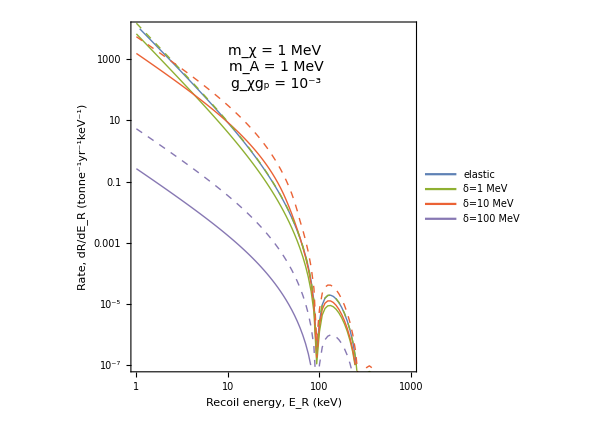
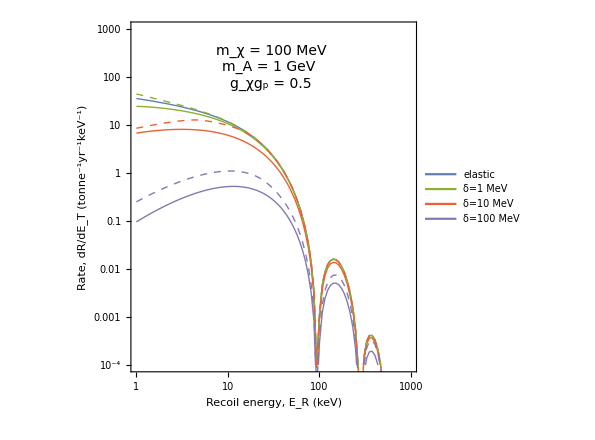

```mathematica
{ratePlot1MeV=Show[
ListLogLogPlot[Join[{datDiffRateVecElas⟦1⟧},datDiffRateVecUpM1MeV],Joined->True,
PlotRange->{{10^0,10^3},{10^-7,10^4}},
FrameTicks->{LogTicks[10^-16,10^12,2],LogTicks[10^0,10^4]},
PlotLegends->Legend[{"elastic","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.82,.85}],
FrameLabel->{"Recoil energy, E_R (keV)","Rate, dR/dE_R (tonne^-1yr^-1keV^-1)"},
PlotStyle->({#,Thick}&/@ColorData[97,"ColorList"][[{1,3,4,5}]]),
GridLines->{{5},None},
Epilog->Inset[Style[" m_χ = 1 MeV \nm_A = 1 MeV\ng_χg_p = 10^-3 ",14,FontFamily->"Times"],Scaled[{.51,.87}]]],
ListLogLogPlot[datDiffRateVecDownM1MeV,Joined->True,
PlotStyle->({#,Thick,Dashed}&/@ColorData[97,"ColorList"][[3;;5]])]
],
ratePlot100MeV=Show[
ListLogLogPlot[Join[{datDiffRateVecElas⟦2⟧},datDiffRateVecUpM100MeV],Joined->True,
FrameTicks->{LogTicks[10^-8,10^12],LogTicks[10^-6,10^3]},
PlotRange->{{10^0,10^3},{10^-4,10^3}},
GridLines->{{5},None},
PlotStyle->({#,Thick}&/@ColorData[97,"ColorList"][[{1,3,4,5}]]),
PlotLegends->Legend[{"elastic","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.82,.85}],
FrameLabel->{"Recoil energy, E_R (keV)","Rate, dR/dE_T (tonne^-1yr^-1keV^-1)"},
Epilog->Inset[Style["   m_χ = 100 MeV\nm_A = 1 GeV \ng_χg_p = 0.5    ",14,FontFamily->"Times"],Scaled[{.49,.87}]]],
ListLogLogPlot[datDiffRateVecDownM100MeV,Joined->True,
PlotStyle->({#,Thick,Dashed}&/@ColorData[97,"ColorList"][[3;;5]])]
]}
```

```mathematica
Export["figures/fig_rate_1MeV.pdf",ratePlot1MeV];
Export["figures/fig_rate_100MeV.pdf",ratePlot100MeV];
```

#### Normalized rate plot

```mathematica
scaledDatDiffRateVecElas=datDiffRateVecElas;
scaledDatDiffRateVecElas⟦1,All,2⟧*=1/datDiffRateVecElas⟦1,24,2⟧;
scaledDatDiffRateVecElas⟦2,All,2⟧*=1/datDiffRateVecElas⟦2,24,2⟧;
```

```mathematica
scaledDatDiffRateVecUpM1MeV=datDiffRateVecUpM1MeV;
scaledDatDiffRateVecUpM1MeV⟦All,All,2⟧*=scaledDatDiffRateVecElas⟦1,24,2⟧/datDiffRateVecUpM1MeV[[All,24,2]];
```

```mathematica
scaledDatDiffRateVecDownM1MeV=datDiffRateVecDownM1MeV;
scaledDatDiffRateVecDownM1MeV⟦All,All,2⟧*=scaledDatDiffRateVecElas⟦1,24,2⟧/datDiffRateVecDownM1MeV[[All,24,2]];
```

```mathematica
scaledDatDiffRateVecUpM100MeV=datDiffRateVecUpM100MeV;
scaledDatDiffRateVecUpM100MeV⟦All,All,2⟧*=scaledDatDiffRateVecElas⟦2,24,2⟧/datDiffRateVecUpM100MeV[[All,24,2]];
```

```mathematica
scaledDatDiffRateVecDownM100MeV=datDiffRateVecDownM100MeV;
scaledDatDiffRateVecDownM100MeV⟦All,All,2⟧*=scaledDatDiffRateVecElas⟦2,24,2⟧/datDiffRateVecDownM100MeV[[All,24,2]];
```

Log scale:

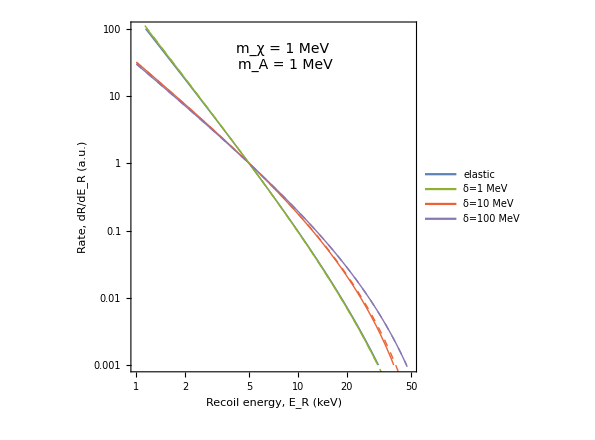
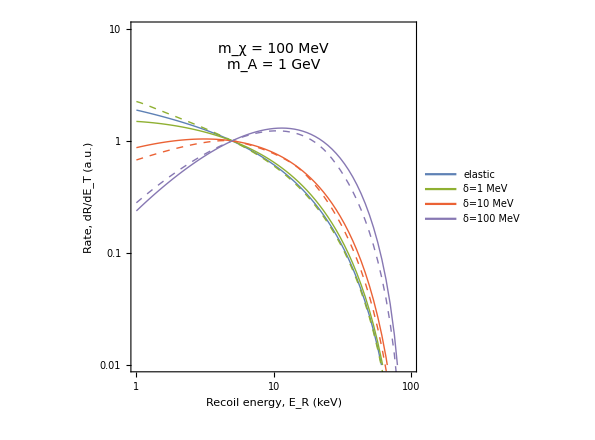

```mathematica
{Show[
ListLogLogPlot[Join[{scaledDatDiffRateVecElas⟦1⟧},scaledDatDiffRateVecUpM1MeV],Joined->True,
PlotRange->{{10^0,50},{10^-3,10^2}},
FrameTicks->{LogTicks[10^-16,10^12],LogTicks[10^0,10^4]},
PlotLegends->Legend[{"elastic","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.82,.85}],
FrameLabel->{"Recoil energy, E_R (keV)","Rate, dR/dE_R (a.u.)"},
PlotStyle->({#,Thick}&/@ColorData[97,"ColorList"][[{1,3,4,5}]]),
GridLines->{{5},None},
Epilog->Inset[Style[" m_χ = 1 MeV \nm_A = 1 MeV",14,FontFamily->"Times"],Scaled[{.54,.9}]]],
ListLogLogPlot[scaledDatDiffRateVecDownM1MeV,Joined->True,
PlotStyle->({#,Thick,Dashed}&/@ColorData[97,"ColorList"][[3;;5]])]
],
Show[
ListLogLogPlot[Join[{scaledDatDiffRateVecElas⟦2⟧},scaledDatDiffRateVecUpM100MeV],Joined->True,
FrameTicks->{LogTicks[10^-8,10^12],LogTicks[10^-4,10^2]},
PlotRange->{{10^0,10^2},{10^-2,10^1}},
GridLines->{{5},None},
PlotStyle->({#,Thick}&/@ColorData[97,"ColorList"][[{1,3,4,5}]]),
PlotLegends->Legend[{"elastic","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.82,.85}],
FrameLabel->{"Recoil energy, E_R (keV)","Rate, dR/dE_T (a.u.)"},
Epilog->Inset[Style["   m_χ = 100 MeV\nm_A = 1 GeV",14,FontFamily->"Times"],Scaled[{.50,.90}]]],
ListLogLogPlot[scaledDatDiffRateVecDownM100MeV,Joined->True,
PlotStyle->({#,Thick,Dashed}&/@ColorData[97,"ColorList"][[3;;5]])]
]}
```

Linear scale:

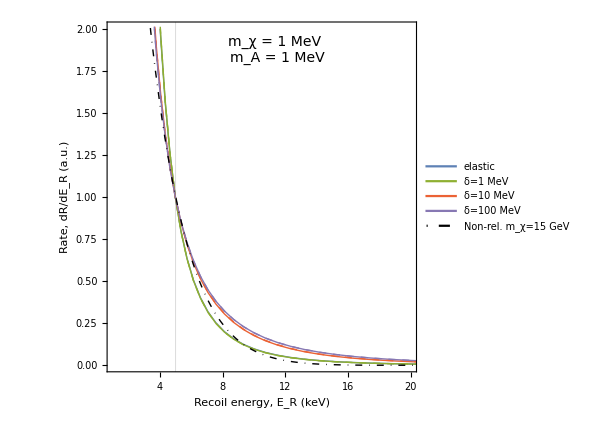
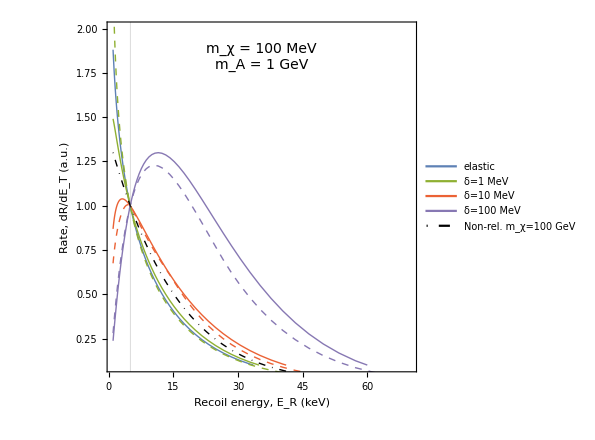

```mathematica
{scaledRatePlot1MeV=Show[
ListPlot[Join[{scaledDatDiffRateVecElas⟦1⟧},scaledDatDiffRateVecUpM1MeV],Joined->True,
PlotRange->{{10^0,20},{10^-3,2}},
PlotLegends->Legend[{"elastic","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.82,.77}],
FrameLabel->{"Recoil energy, E_R (keV)","Rate, dR/dE_R (a.u.)"},
PlotStyle->({#,Thick}&/@ColorData[97,"ColorList"][[{1,3,4,5}]]),
GridLines->{{5},None},
Epilog->Inset[Style[" m_χ = 1 MeV \nm_A = 1 MeV",14,FontFamily->"Times"],Scaled[{.55,.92}]]],
ListPlot[scaledDatDiffRateVecDownM1MeV,Joined->True,
PlotStyle->({#,Thick,Dashed}&/@ColorData[97,"ColorList"][[3;;5]])],
Plot[dRdEr[Er 10^-6,0,131,15,1,1]/dRdEr[5 10^-6,0,131,15,1,1],{Er,1,60},PlotStyle->{Black,DotDashed,Thick},PlotRange->All,PlotLegends->Legend[{"Non-rel.      \n  m_χ=15 GeV"},Position->{.835,.94},LegendMarkerSize->21]]
],
scaledRatePlot100MeV=Show[
ListPlot[Join[{scaledDatDiffRateVecElas⟦2⟧},scaledDatDiffRateVecUpM100MeV],Joined->True,
PlotRange->{{10^0,70},{10^-1,2}},
GridLines->{{5},None},
PlotStyle->({#,Thick}&/@ColorData[97,"ColorList"][[{1,3,4,5}]]),
PlotLegends->Legend[{"elastic","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.82,.75}],
FrameLabel->{"Recoil energy, E_R (keV)","Rate, dR/dE_T (a.u.)"},
Epilog->Inset[Style["   m_χ = 100 MeV\nm_A = 1 GeV",14,FontFamily->"Times"],Scaled[{.50,.90}]]],
ListPlot[scaledDatDiffRateVecDownM100MeV,Joined->True,
PlotStyle->({#,Thick,Dashed}&/@ColorData[97,"ColorList"][[3;;5]])],
Plot[dRdEr[Er 10^-6,0,131,100,1,1]/dRdEr[5 10^-6,0,131,100,1,1],{Er,1,60},PlotStyle->{Black,DotDashed,Thick},PlotLegends->Legend[{"Non-rel.        \n m_χ=100 GeV"},Position->{.835,.92},LegendMarkerSize->21]]
]}
```

```mathematica
Export["figures/fig_rateScaled_1MeV.pdf",scaledRatePlot1MeV];
Export["figures/fig_rateScaled_100MeV.pdf",scaledRatePlot100MeV];
```

## XENON1t bounds

### Total rates in XENON1T

Define efficiency function, returns fraction of events observed for a given recoil energy
	ErkeV = recoil energy in keV

```mathematica
xeEff[ErkeV_]:=.5(0.44*Erfc[.3*(5.4-ErkeV)]*0.5*Erfc[.14*(ErkeV-42)])
```

Total event rate fucntions in XENON1T for:
 - non-relativistic DM: 
 - endothermic CRDM scattering:
 - exothermic CRDM scattering:
	mx = dark matter mass in GeV
	δ = mass splitting in GeV
	gxi = coupling 
	mA = mass of mediator in GeV
Rate is returned with units /tonne/yr

```mathematica
NReventsXe1t[mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,mA_?NumericQ]:=
If[((μ[131amu,mx]((vesc+ve)/c)^2)/2<δ)||(VminGlobal[δ,mx,131 amu]>(ve+vesc)/c),0,
NIntegrate[
dRdErFull[Er,δ,131,mx,gxi,mA] 10^6,
{Er,Max[2 10^-6,ErMinGeV[δ,VMAX,mx,131amu]],ErMaxGeV[δ,VMAX,mx,131amu]},
PrecisionGoal->3]]
```

```mathematica
iCRDMeventsXe1tU[mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,mA_?NumericQ,nPoints_:50]:=
Module[{rate},

rate=Interpolation[
dRdErUpList[Max[ErMinU[TXMAX,mx,δ,131amu],2 10^-6],Min[ErMaxU[TXMAX,mx,δ,131amu],60 10^-6],mx,δ,gxi,mA,nPoints]
,InterpolationOrder->1];

NIntegrate[
xeEff[ErkeV]rate[ErkeV],
{ErkeV,10^6 Max[ErMinU[TXMAX,mx,δ,131amu],2 10^-6],10^6 Min[ErMaxU[TXMAX,mx,δ,131amu],60 10^-6]},
PrecisionGoal->2]//Return;
];
```

```mathematica
iCRDMeventsXe1tD[mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,mA_?NumericQ,nPoints_:50]:=
Module[{rate},

rate=Interpolation[
dRdErDownList[Max[ErMinD[TXMAX,mx,δ,131amu],2 10^-6],Min[ErMaxD[TXMAX,mx,δ,131amu],60 10^-6],mx,δ,gxi,mA,nPoints],
InterpolationOrder->1];

NIntegrate[
xeEff[ErkeV]rate[ErkeV],
{ErkeV,10^6 Max[ErMinD[TXMAX,mx,δ,131amu],2 10^-6],10^6 Min[ErMaxD[TXMAX,mx,δ,131amu],60 10^-6]},
PrecisionGoal->2]//Return;
];
```

### Sensitivity in mass vs. coupling

Assuming a 1t.y exposure, based on the second column of table I of 1805.12562:

```mathematica
Nexp=7.36;
Nobs=14;
```

```mathematica
logL[x_,bgexp_,obs_,bgN_]=-(bgexp bgN+x)+obs Log[bgexp bgN+x]-Log[obs!]+Log[PDF[NormalDistribution[1,.15],bgN]];
```

Find the 90%CL:

```mathematica
sol=FindMinimum[{(√(-2(logL[x,Nexp,Nobs,1]-logL[Nobs-Nexp,Nexp,Nobs,1]))-InverseCDF[NormalDistribution[0,1],0.9])^2,x>1},{x,10}]
```

{3.66198×10^-16,{x→11.9975}}

```mathematica
NupperLimit=x/.sol[[2]];
```

We use 12 events as the upper limit.

#### Calculations

CRDM upscattering bounds:

```mathematica
With[{MA=1,npoints=100},
xe1tDatiCRDMmxGGheavMedU={
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tU[mx,.0001,1,MA,npoints]+10^-100)))},{mx,logSpace[.001,10^2,100]}],
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tU[mx,.001,1,MA,npoints]+10^-100)))},{mx,logSpace[.0001,100,100]}],
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tU[mx,.010,1,MA,npoints]+10^-100)))},{mx,logSpace[.0001,40,100]}],
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tU[mx,.100,1,MA,npoints]+10^-100)))},{mx,logSpace[.0001,2,100]}]};
]
```

```mathematica
del={"p0001","p001","p01","p1"};
Table[Export["Xe1t_bounds_heavyMed_del"<>del[[ii]]<>"_up.csv",xe1tDatiCRDMmxGGheavMedU[[ii]]],{ii,1,4}];
```

```mathematica
With[{MA=.001,npoints=100},
xe1tDatiCRDMmxGGlightMedU={
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tU[mx,.0001,1,MA,npoints]+10^-100)))},{mx,logSpace[.001,100,100]}],
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tU[mx,.001,1,MA,npoints]+10^-100)))},{mx,logSpace[.0001,100,100]}],
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tU[mx,.010,1,MA,npoints]+10^-100)))},{mx,logSpace[.0001,100,100]}],
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tU[mx,.100,1,MA,npoints]+10^-100)))},{mx,logSpace[.0001,100,100]}]};
]
```

```mathematica
del={"p0001","p001","p01","p1"};
Table[Export["Xe1t_bounds_lightMed_del"<>del[[ii]]<>"_up.csv",xe1tDatiCRDMmxGGlightMedU[[ii]]],{ii,1,4}];
```

CRDM downscattering bounds:

```mathematica
With[{MA=1,npoints=60},
xe1tDatiCRDMmxGGheavMedD={
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tD[mx,   0,1,MA,npoints]+10^-100)))},{mx,logSpace[.0001,100,100]}],
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tD[mx,.0001,1,MA,npoints]+10^-100)))},{mx,logSpace[.001,100,100]}],
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tD[mx,.001,1,MA,npoints]+10^-100)))},{mx,logSpace[.0001,100,100]}],
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tD[mx,.010,1,MA,npoints]+10^-100)))},{mx,logSpace[.0001,  40,100]}],
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tD[mx,.100,1,MA,npoints]+10^-100)))},{mx,logSpace[.0001,   2,100]}]};
]
```

```mathematica
del={"0","p0001","p001","p01","p1"};
Table[Export["Xe1t_bounds_heavyMed_del"<>del[[ii]]<>"_down.csv",xe1tDatiCRDMmxGGheavMedD[[ii]]],{ii,1,5}];
```

```mathematica
With[{MA=.001,npoints=60},
xe1tDatiCRDMmxGGlightMedD={
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tD[mx,    0,1,MA,npoints]+10^-100)))},{mx,logSpace[.0001,100,100]}],
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tD[mx,.0001,1,MA,npoints]+10^-100)))},{mx,logSpace[.0001,100,100]}],
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tD[mx, .001,1,MA,npoints]+10^-100)))},{mx,logSpace[.0001,100,100]}],
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tD[mx, .010,1,MA,npoints]+10^-100)))},{mx,logSpace[.0001,100,100]}],
Table[{mx,√(√(NupperLimit /(iCRDMeventsXe1tD[mx, .100,1,MA,npoints]+10^-100)))},{mx,logSpace[.0001,1,100]}]};
]
```

```mathematica
del={"0","p0001","p001","p01","p1"};
Table[Export["Xe1t_bounds_lightMed_del"<>del[[ii]]<>"_down.csv",xe1tDatiCRDMmxGGlightMedD[[ii]]],{ii,1,5}];
```

#### Import previously calculated bounds

```mathematica
NotebookDirectory[]//SetDirectory;
```

```mathematica
del={"p0001","p001","p01","p1"};
xe1tDatiCRDMmxGGheavMedU=Table[Import["results/Xe1t_bounds_heavyMed_del"<>del[[ii]]<>"_up.csv"],{ii,1,4}];
xe1tDatiCRDMmxGGlightMedU=Table[Import["results/Xe1t_bounds_lightMed_del"<>del[[ii]]<>"_up.csv"],{ii,1,4}];
```

```mathematica
del={"0","p0001","p001","p01","p1"};
xe1tDatiCRDMmxGGheavMedD=Table[Import["results/Xe1t_bounds_heavyMed_del"<>del[[ii]]<>"_down.csv"],{ii,1,5}];
xe1tDatiCRDMmxGGlightMedD=Table[Import["results/Xe1t_bounds_lightMed_del"<>del[[ii]]<>"_down.csv"],{ii,1,5}];
```

#### Plot sensitivity

```mathematica
label[x_,y_,z_]:=Text[Superscript[10,z],{x,y},Background->White]
```

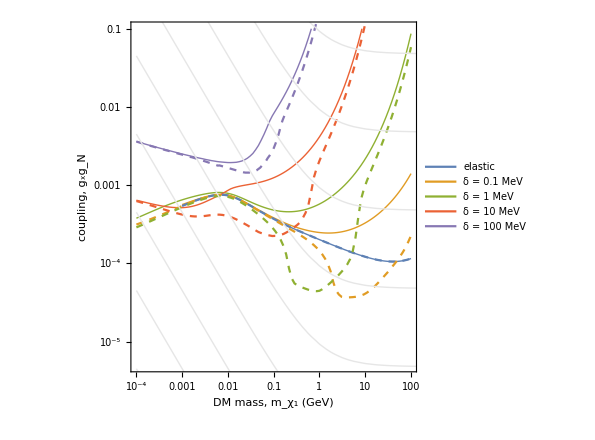
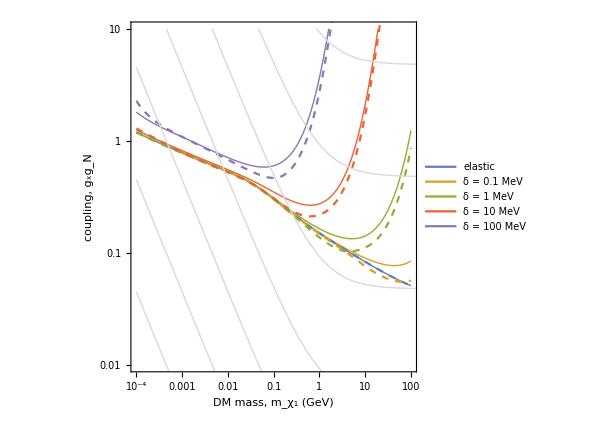

```mathematica
{boundPlotMed1MeV=Show[ListLogLogPlot[Join[{xe1tDatiCRDMmxGGlightMedD⟦1⟧},xe1tDatiCRDMmxGGlightMedU],Joined->True,
PlotRange->{{.0001,10^2},{5 10^-6,10^-1}},
PlotLegends->Legend[{"elastic","δ = 0.1 MeV","δ = 1 MeV","δ = 10 MeV","δ = 100 MeV"},Position->{.22,.22}],
FrameLabel->{{"coupling, g_xg_N","(σ̃)_0 (cm^2)"},{"DM mass, m_χ_1 (GeV)",""}},
FrameTicks->{{LogTicks[10^-5,10^3]⟦1⟧,Table[{gg[10^x,100,.001]^2,Superscript[10,x]},{x,-42,-14,2}]},LogTicks[10^-4,10^2]}],
ListLogLogPlot[xe1tDatiCRDMmxGGlightMedD,Joined->True,PlotStyle->Dashed],
ContourPlot[σXP[√gg,mx,.001]//Log10,{mx,10^-4,10^3},{gg,10^-6,10},
Contours->Range[-38,-14,2],ScalingFunctions->{"Log","Log"},ContourShading->None,ContourStyle->Lighter[Gray,.8]]
],
boundPlotMed1GeV=Show[
ListLogLogPlot[Join[{xe1tDatiCRDMmxGGheavMedD⟦1⟧},xe1tDatiCRDMmxGGheavMedU],Joined->True,
PlotRange->{{.0001,10^2},{10^-2,10^1}},
PlotLegends->Legend[{"elastic","δ = 0.1 MeV","δ = 1 MeV","δ = 10 MeV","δ = 100 MeV"},Position->{.22,.22}],
FrameLabel->{{"coupling, g_xg_N","(σ̃)_0 (cm^2)"},{"DM mass, m_χ_1 (GeV)",""}},
FrameTicks->{{LogTicks[10^-4,10^1]⟦1⟧,Table[{gg[10^x,100,1]^2,Superscript[10,x]},{x,-42,-20,2}]},LogTicks[10^-4,10^3]}],
ListLogLogPlot[xe1tDatiCRDMmxGGheavMedD,Joined->True,PlotStyle->Dashed],
ContourPlot[σXP[√g,mx,1]//Log10,{mx,10^-4,10^3},{g,10^-4,10},
Contours->Range[-38,-26,2],ScalingFunctions->{"Log","Log"},ContourShading->None,ContourStyle->Lighter[Gray,.7]]
]}
```

```mathematica
Export["./figures/fig_bound_m1GeV.pdf",boundPlotMed1GeV];
Export["./figures/fig_bound_m1MeV.pdf",boundPlotMed1MeV];
```

### Attenuation

In this section we approximate the attenuation of the CRDM before reaching XENON1t at LNGS.

We estimate attenuation for the elastic case only and find the coupling which would attenuate 10GeV dark matter to below threshold.

Depth of LNGS:

```mathematica
Zlngs=140000 Centimeter GeV;
```

Approximate composition of the crust from Kouvaris and Emken:

```mathematica
NA=6.02 10^23/mol;
ρE=2.7g/Centimeter^3;
AN={16,28,27,56,40,39,23,24};
nN=ρE NA{(.466)/(16 g/mol),(.277)/(28 g/mol),(.081)/(27 g/mol),(.05)/(55.85 g/mol),(.036)/(40 g/mol),(.028)/(39.1 g/mol),(.026)/(23 g/mol),(.021)/(24.3 g/mol)};(*nuclei/cm^3*)
```

Average these as an effective density and atomic mass (see appendix for validity):

```mathematica
avgN=ρE NA Plus@@{(.466)/(16 g/mol),(.277)/(28 g/mol),(.081)/(27 g/mol),(.05)/(55.85 g/mol),(.036)/(40 g/mol),(.028)/(39.1 g/mol),(.026)/(23 g/mol),(.021)/(24.3 g/mol)} ;
avgA=Plus@@{.466 16,28 .277,27 .081,56 .05,40 .036,39 .028,23 .026,24 .021};
```

Define energy loss function:

```mathematica
dTdzUpApprox[Txx_?NumericQ,mx_?NumericQ,δ_?NumericQ,gx_?NumericQ,mA_?NumericQ]:=
NIntegrate[avgN Er dσdErUp[Er,Txx,avgA,mx,δ,gx,mA],{Er,ErMinU[Txx,mx,δ,avgA mp],ErMaxU[Txx,mx,δ,avgA mp]},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->3,AccuracyGoal->Infinity] GeV^2
```

Solving the energy loss DE:

```mathematica
TxLNGS[TxSurface_?NumericQ,mx_?NumericQ,δ_?NumericQ,gx_?NumericQ,mA_?NumericQ]:=
Module[{Tx},
NDSolveValue[{D[Tx[z],z]==-dTdzUpApprox[Tx[z],mx,δ,gx,mA] GeV^-2,Tx[0]==TxSurface},Tx[Zlngs],{z,0,Zlngs},PrecisionGoal->3,AccuracyGoal->8]//# HeavisideTheta[#]&//Return]
```

```mathematica
With[{mA=.001},
gx=.435;
attenDat10=Table[{mx,
TxZ=TxLNGS[10,mx,0,gx,mA];
While[TxZ>TxMinEd[5 10^-6,131amu,mx,0],
gx*=1.0025;
TxZ=TxLNGS[10,mx,0,gx,mA];];
gx^2},
{mx,logSpace[.0001,10,30]//Reverse}
]];
```

### Fermi bounds

```mathematica
fermiIGRB=Import["data/FERMI_IGRB.csv"];
```

```mathematica
With[{MA=1,gx=1,EMIN=.119,EMAX=30.49,nPoints=17},
fermiLimitHeavy=Table[{MX,dϕγdElist[EMIN,EMAX,MX,δ,gx,MA,nPoints]//√(fermiIGRB[[1;;17,2]]/(#[[All,2]] 1/(4π)GeV (unitsCM2S cm^2 s) (#⟦All,1⟧)^2+10^-100))&//Min}
,{δ,{.001,.01,.1}}
,{MX,logSpace[10^-4,10,20]}]
];
```

```mathematica
With[{MA=.001,gx=1,EMIN=fermiIGRB[[1,1]],EMAX=fermiIGRB[[-1,1]],nPoints=Length[fermiIGRB]},
fermiLimitLight=
Table[{MX,dϕγdElist[EMIN,EMAX,MX,δ,gx,MA,nPoints]//√(fermiIGRB[[All,2]]/(#[[All,2]] 1/(4π)GeV (unitsCM2S cm^2 s) (#⟦All,1⟧)^2+10^-100))&//Min}
,{δ,{.0001,.001,.01,.1}}
,{MX,logSpace[10^-4,10,30]}]
];
```

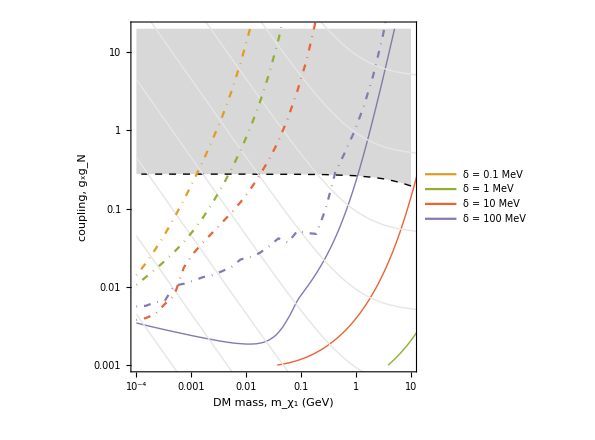

```mathematica
fermiBoundPlot=Show[
ListLogLogPlot[xe1tDatiCRDMmxGGlightMedU,Joined->True,
PlotRange->{{.0001,10},{10^-3,20}},
PlotLegends->Legend[{"δ = 0.1 MeV","δ = 1 MeV","δ = 10 MeV","δ = 100 MeV"},Position->{.2,.85}],
FrameLabel->{{"coupling, g_xg_N","(σ̃)_0 (cm^2)"},{"DM mass, m_χ_1 (GeV)",""}},
PlotStyle->({#,Thick}&/@ColorData[97,"ColorList"][[{2,3,4,5}]]),
FrameTicks->{{LogTicks[10^-5,10^3]⟦1⟧,Table[{gg[10^x,100,.001]^2,Superscript[10,x]},{x,-42,-14,2}]},LogTicks[10^-4,10^2]}],
ListLogLogPlot[attenDat10,Joined->True,
PlotStyle->{Thick,Black,Dashed},
Filling->Top,FillingStyle->Opacity[.3,Gray],
PlotRange->{.1,20}],
ContourPlot[σXP[√gg,mx,.001]//Log10,{mx,10^-4,10^3},{gg,10^-6,100},
Contours->Range[-38,-14,2],ScalingFunctions->{"Log","Log"},ContourShading->None,ContourStyle->Lighter[Gray,.8]],ListLogLogPlot[Join[{{{0,0},{0,0}}},fermiLimitLight],PlotStyle->DotDashed,Joined->True]]
```

```mathematica
Export["figures/fig_fermi_atten.pdf",fermiBoundPlot]
```

figures/fig_fermi_atten.pdf

## Appendix

### Cross sections

Since δ is small the cross sections are degenerate, therefore the differences in the rate come from the flux and kinematics.

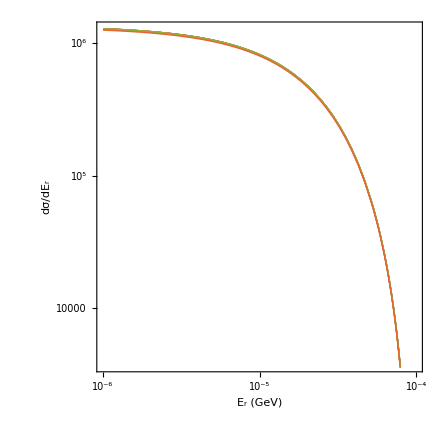
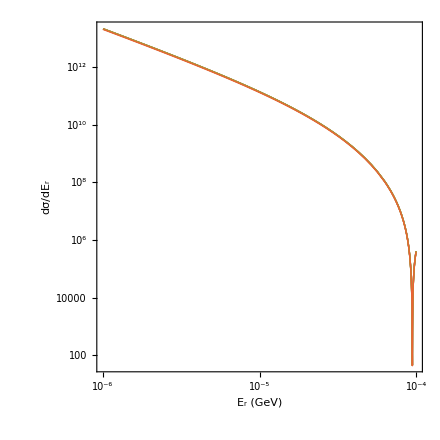

```mathematica
{With[{Tx1=1,mx=.1,MA=1,gxi=1},
Show[LogLogPlot[{dσdErUp[ErGeV,Tx1,131,mx,0,gxi,MA] GeV^3,dσdErUp[ErGeV,Tx1,131,mx,.001,gxi,MA] GeV^3,dσdErUp[ErGeV,Tx1,131,mx,.01,gxi,MA] GeV^3,dσdErUp[ErGeV,Tx1,131,mx,.1,gxi,MA] GeV^3},{ErGeV,10^-6,10^-4},
FrameTicks->{LogTicks[10^0,10^14,1],LogTicks[10^-6,10^-4]},
FrameLabel->{"E_r (GeV)","dσ/dE_r"}],
LogLogPlot[{dσdErDown[ErGeV,Tx1,131,mx,0,gxi,MA] GeV^3,dσdErDown[ErGeV,Tx1,131,mx,.001,gxi,MA] GeV^3,dσdErDown[ErGeV,Tx1,131,mx,.01,gxi,MA] GeV^3,dσdErDown[ErGeV,Tx1,131,mx,.1,gxi,MA] GeV^3},{ErGeV,10^-6,10^-4}]]]
,
With[{Tx1=1,mx=.001,MA=.001,gxi=1},Show[LogLogPlot[{dσdErUp[ErGeV,Tx1,131,mx,0,gxi,MA] GeV^3,dσdErUp[ErGeV,Tx1,131,mx,.001,gxi,MA] GeV^3,dσdErUp[ErGeV,Tx1,131,mx,.01,gxi,MA] GeV^3,dσdErUp[ErGeV,Tx1,131,mx,.1,gxi,MA] GeV^3},{ErGeV,10^-6,10^-4},
FrameTicks->{LogTicks[10^0,10^14,1],LogTicks[10^-6,10^-4]},
FrameLabel->{"E_r (GeV)","dσ/dE_r"}],
LogLogPlot[{dσdErDown[ErGeV,Tx1,131,mx,0,gxi,MA] GeV^3,dσdErDown[ErGeV,Tx1,131,mx,.001,gxi,MA] GeV^3,dσdErDown[ErGeV,Tx1,131,mx,.01,gxi,MA] GeV^3,dσdErDown[ErGeV,Tx1,131,mx,.1,gxi,MA] GeV^3},{ErGeV,10^-6,10^-4}]]]}
```

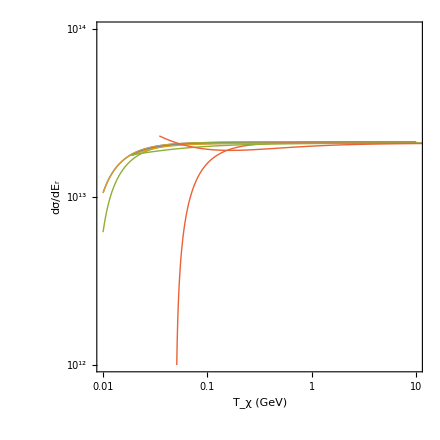

```mathematica
With[{ErGeV=10^-6,mx=.001,MA=.001,gxi=1},Show[LogLogPlot[{dσdErUp[ErGeV,Tx1,131,mx,0,gxi,MA] GeV^3,dσdErUp[ErGeV,Tx1,131,mx,.001,gxi,MA] GeV^3,dσdErUp[ErGeV,Tx1,131,mx,.01,gxi,MA] GeV^3,dσdErUp[ErGeV,Tx1,131,mx,.1,gxi,MA] GeV^3},{Tx1,10^-2,10^1},
PlotRange->{10^12,10^14},
FrameTicks->{LogTicks[10^12,10^14],LogTicks[10^-3,10^3]},
FrameLabel->{"T_χ (GeV)","dσ/dE_r"}],
LogLogPlot[{dσdErDown[ErGeV,Tx1,131,mx,0,gxi,MA] GeV^3,dσdErDown[ErGeV,Tx1,131,mx,.001,gxi,MA] GeV^3,dσdErDown[ErGeV,Tx1,131,mx,.01,gxi,MA] GeV^3,dσdErDown[ErGeV,Tx1,131,mx,.1,gxi,MA] GeV^3},{Tx1,10^-3,10^3}]]]
```

### Kinematics Plots

```mathematica
kinDatU=Table[
{mx,TxMinEu[5 10^-6,131,mx,δ]},
{δ,{0,.0001,.001,.01,.1}},
{mx,logSpace[.0001,100,30]}];
```

```mathematica
kinDatD=Table[
{mx,TxMinEd[5 10^-6,131,mx,δ]},
{δ,{0,.0001,.001,.01,.1}},
{mx,logSpace[.0001,100,100]}];
```

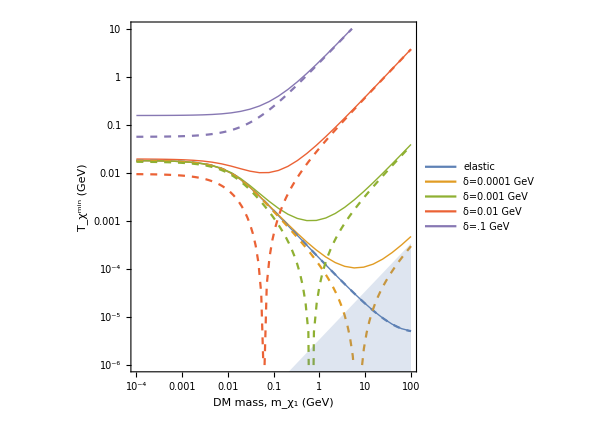

```mathematica
Show[
ListLogLogPlot[kinDatU,Joined->True,
PlotRange->{{10^-4,100},{10^-6,10}},
FrameTicks->{LogTicks[10^-6,10^1,2],LogTicks[10^-4,10^2]},
PlotLegends->Legend[{"elastic","δ=0.0001 GeV","δ=0.001 GeV","δ=0.01 GeV","δ=.1 GeV"},Position->{.2,.2}],
FrameLabel->{"DM mass, m_χ_1 (GeV)","T_χ^min (GeV)"}],
ListLogLogPlot[kinDatD,Joined->True,PlotStyle->Dashed,
PlotRange->{{10^-4,100},{10^-6,10}}],
LogLogPlot[1/2 mx VMAX^2,{mx,10^-4,100},PlotStyle->None,Filling->Bottom]]
```

Find an expression for the minima in the exothermic case:

```mathematica
0==(Er (2 Er mT-4 mT (mx+δ)-δ (2 mx+δ))+√(Er (Er+2 mT) (2 Er mT+δ^2) (2 Er mT+(2 mx+δ)^2)))/(4 Er mT)//Solve[#,mx]&
```

{{mx→(-2 Er mT-2 Er δ+δ^2)/(2 (Er-δ))}}

```mathematica
mxTxMin[Er_,mT_,δ_]:=(-2 Er mT-2 Er δ+δ^2)/(2 (Er-δ))
```

```mathematica
mxTxMin[Er_,mT_,δ_]:=(Er mT)/(δ)
```

```mathematica
(10 10^-6 131 amu)/(δ)
```

0.00122025727/δ

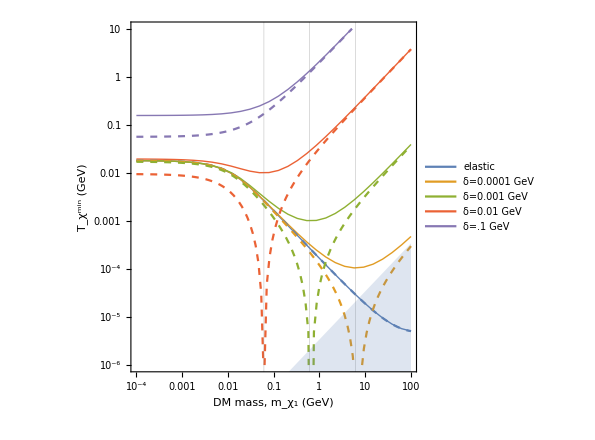

```mathematica
Show[
ListLogLogPlot[kinDatU,Joined->True,
PlotRange->{{10^-4,100},{10^-6,10}},
FrameTicks->{LogTicks[10^-6,10^1,2],LogTicks[10^-4,10^2]},
PlotLegends->Legend[{"elastic","δ=0.0001 GeV","δ=0.001 GeV","δ=0.01 GeV","δ=.1 GeV"},Position->{.2,.2}],
FrameLabel->{"DM mass, m_χ_1 (GeV)","T_χ^min (GeV)"},
GridLines->{{mxTxMin[5 10^-6,131amu,.01],mxTxMin[5 10^-6,131amu,.001],mxTxMin[5 10^-6,131amu,.0001]},None}],
ListLogLogPlot[kinDatD,Joined->True,PlotStyle->Dashed,
PlotRange->{{10^-4,100},{10^-6,10}}],
LogLogPlot[1/2 mx VMAX^2,{mx,10^-4,100},PlotStyle->None,Filling->Bottom]]
```